# Quartic-scalar-Gauss-Bonnet theory

## 1. Integration: main functions

### Spontaneous scalarization (ℱ’[0]=0)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]; (*imposto la directory del current evaluation notebook*)
```

```mathematica
(*Loading the system of equations from auxiliary file*)(*importo i file contenenti le equazioni differenziali che mi interessano*)
```

```mathematica
EQSEDGB=Import["general_edgb_systemeqs.m"];
backEQS=Import["../Stability/Data/general_background_eqs.m"];
BEQS=Simplify[backEQS//.{Vf->(0&),α->1/2}];
```

```mathematica
(*Load packages for numerical integration*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

```mathematica
(*Define the coupling function we will study*)
```

```mathematica
ruleQuartic={ℱ-> ((η/8#^2+λ/16#^4)&)};
```

### Background boundary conditions

```mathematica
(*Clear[A,B,ϕ]*)
```

Faccio uno sviluppo delle funzioni metriche e del campo scalare in funzione di r-rh all’orizzonte

```mathematica
(*A[r_]:=Sum[Subscript[ai, i](r-1)^i,{i,1,5}];
B[r_]:=Sum[Subscript[bi, i](r-1)^i,{i,1,5}];
ϕ[r_]:=Sum[Subscript[fi, i](r-1)^i,{i,0,5}];*)
```

Ottengo lo sviluppo delle equazioni per il background all’orizzonte

```mathematica
(*eqshor=Series[{BEQS[[1]],BEQS[[2]],BEQS[[3]](r-1)},{r,1,4}];*)
```

```mathematica
(*eqshor1=Table[SeriesCoefficient[eqshor[[i]],0],{i,1,3}];
eqshor2=Table[SeriesCoefficient[eqshor[[i]],1],{i,1,3}];*)
```

```mathematica
(*eqshor1[[3]]//Simplify*)
```

```mathematica
(*shor1=Solve[eqshor1==0,{Subscript[fi, 1],Subscript[bi, 1]}][[2]];
shor2=Solve[eqshor2==0,{Subscript[fi, 2],Subscript[bi, 2],Subscript[ai, 2]}][[1]];*)
```

```mathematica
(*shor1[[1]]//Simplify*)
```

Joining the rules for the background

```mathematica
(*shorf=Join[shor1,shor2];*)
```

Boundary condition for the background at the horizon. We shall consider only terms up to second order.

```mathematica
(*bouhor={Sum[Subscript[ai, i](r-1)^i,{i,1,2}],Sum[Subscript[bi, i](r-1)^i,{i,1,2}],Sum[Subscript[fi, i](r-1)^i,{i,0,2}],D[Sum[Subscript[fi, i](r-1)^i,{i,0,2}],r]};*)
```

```mathematica
(*bouhor[[3]]*)
```

```mathematica
(*BEQS[[1]]/.ruleQuartic/.r->10*)
```

```mathematica
(*SetPrecision[N[1/(1-2*10^-16)],20]*)
```

```mathematica
(*Clear[sGBINT]*)
```

```mathematica
BCSbckHor=<<"../Stability/Data/expanded_bck_BCS_hor.m";
```

Boundary condition for the background at the horizon. We shall consider only terms up to second order.

```mathematica
bouhor={Sum[Subscript[ai, i](r-1)^i,{i,1,2}],Sum[Subscript[bi, i](r-1)^i,{i,1,2}],Sum[Subscript[fi, i](r-1)^i,{i,0,2}],D[Sum[Subscript[fi, i](r-1)^i,{i,0,2}],r]};
```

```mathematica
Clear[A,B,ϕ]
```

```mathematica
sGBINT[rh0_,phic0_,η0_,λ0_,rmax0_,NHorizons0_,MODEL_]:=(
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->15,AccuracyGoal->15,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*How far from the horizon we will start our integrations*)
ϵ=2*10^-16;
BChorrule=BCSbckHor//.F->ℱ//.MODEL;
ruBChor=BChorrule//.{η->η0,λ->λ0}/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOU=Thread[{A[r],B[r],ϕ[r], ϕ'[r]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0)]/.r->rh0+ϵ;
(*Initial conditions
 The equation of motion have the form Υ''[Υ'[r],Φ'[r]], Φ''[Υ'[r],Φ'[r]] so we 
 only need initial conditions for Υ and Φ. *)

(*(*mi fermo al primo ordine in espansione intorno all'orizzonte*)
BCS={
A[r]==N[r-rh],
B[r]==N[r-rh],
ϕ'[r]==N[(rh/(4 F'[ϕ[r]]))(-1+Sqrt[1-96 ((F'[ϕ[r]])^2/rh^4)])]//.F->ℱ//.Union[MODEL,{η->η0, λ->λ0}],
(*condizione necessaria affinché ϕ'' non diverga all'orizzonte.*)
ϕ[r]==phic0
}//.{r->rh0+ϵ,rh-> rh0,η-> η0, λ->λ0,ϕ[rh]->phic0};*)
BCS=BOU;
(*Numerical integration*)
sol=NDSolve[
Union[Union[{BEQS[[2]]==0,BEQS[[1]]==0, BEQS[[3]]==0}//.F->ℱ//.Union[MODEL,{η->η0, λ->λ0}]],BCS],
{A,B,ϕ},
{r,rh0+ϵ,rmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsol=ϕ[r]/.sol;
Dϕsol=D[ϕsol,r];
Asol=A[r]/.sol;
DAsol=D[Asol,r];
Bsol=B[r]/.sol;
DBsol=D[Bsol,r];
(*Values of variables at infinity*)
ϕinf=ϕsol/.{r-> rmax0};
Ainf=Asol/.{r-> rmax0};
Binf=Bsol/.{r-> rmax0};
Asolshift=Asol/Ainf;

(*Extract physical parameters of the BH solution*)
PhysicalParams=NSolve[{
Asolshift==1-(2 M)/r+((M Q^2)/(12 r^3)),
ϕsol==ϕ0+Q/r+(M Q)/r^2+((32 M^2 Q-Q^3)/(24 r^3)),
D[ϕsol,r]==D[ϕ0+Q/r+(M Q)/r^2,r]&&M≥ 0 }/.{r->rh0*NHorizons0},{ϕ0,Q,M}][[1]];

(*NOTA: entrambe le costanti di accoppiamento η e λ hanno (dimensione [length])^2, mentre il campo scalare à adimensionale in tale trattazione e lo scalare di Gauss-Bonnet (è [length])^-4*)
(*Nell'output restituisco l'esponenziale delle funzioni metriche Υ e Λ, che chiamo A[r] e B[r]*)

(*Output: ϕ0, ϕinf, Q/M, η/M^2, λ/M^2, M, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r]*)

{N[rh0/M]/.PhysicalParams,
ϕ0/.PhysicalParams,
ϕinf,
(Q/M)/.PhysicalParams,
(η0/M^2)/.PhysicalParams,
(λ0/M^2)/.PhysicalParams,
M/.PhysicalParams,
ϕsol,
Dϕsol,
Asol/Ainf,
DAsol/Ainf,
Bsol(*/Binf*),
DBsol(*/Binf*)
}
);
Rh=1; (*The value for the event horizon I will use for each function*)
```

```mathematica
Clear[QsGBINT]; (*azzero i parametri iniziali per lintegrazione delle gb-equations*)
```

```mathematica
(*i parametri iniziali che do in pasto a tale funzione sono: raggio e campo scalare all'orizzonte (rh e ϕh); costanti di accoppiamento η e λ tra campo e termine di Gauss-Bonnet, rispettivamente del termine quadratico e del termine quartico; valore massimo a cui arrivo del raggio, Nh non so che sia e infine il model è il tipo di rule che mi definisce l'accoppiamento.
La funzione mi restituisce in output:
raggio e campo scalare all'orizzonte (rh e ϕh), valore del campo scalare all'infinito Φinf,
 carica scalare(come costante di integrazione Q) su M, massa del buco nero, e infine l'andamento del campo scalre in funzione della distanza dal buco nero Φ[r] *)
```

QsGBINT:   (rh,ϕh,η,λ,rmax,Nh,rule) ->  (rh,ϕh,ϕinf,Q/M,η,λ,M,ϕ[r])    Integration of the equations for a given choice of rh, ϕh, η

```mathematica
QsGBINT[rh0_,phic0_,η0_,λ0_,rmax0_,NHorizons0_,MODEL_]:=(
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->12,AccuracyGoal->12,InterpolationOrder->All,Method->"StiffnessSwitching"};

(*How far from the horizon we will start our integrations*)
ϵ=10^-5;

(*Initial conditions
 The equation of motion have the form Υ''[Υ'[r],Φ'[r]], Φ''[Υ'[r],Φ'[r]] so we 
 only need initial conditions for Υ and Φ. 
Υ non è altro che la funzione metrica della parte temporale della metrica a simmetria sferica che abbiamo assunto come background. Verso l'orizzonte si presuppone che in coordinate radiali exp(-Υ) diverga*)

(*mi fermo al primo ordine in espansione intorno all'orizzonte*)
BCS={
Υ'[r]==N[1/(r-rh)],
Υ[r]==N[Log[r-rh]],
Φ'[r]==N[ -rh/(Φ[rh] (η+λ  (Φ[rh])^2))(1-Sqrt[1-(6(Φ[rh])^2)/rh^4(η+λ(Φ[rh])^2)^2])],
(*condizione necessaria affinché Φ'' non diverga all'orizzonte. Espressione presa da articolo 1812.05590.
L'espressione più generale sarebbe:
	N[(rh/(4 ℱ'[Φ[r]]))(-1+Sqrt[1-96 ((ℱ'[Φ[r]])^2/rh^4)])]
*)
Φ[r]==phic0
}//.{r->rh0+ϵ,rh-> rh0,η-> η0, λ->λ0,Φ[rh]->phic0};

(*Print[BCS];*)

(*Definisco prima le equazioni da risolvere con la quartic rule*)
(*QsGB=EQSEDGB//.MODEL;*) (*sta per quartic scalar Gauss-Bonnet*)

(*Numerical integration*)
sol=NDSolve[
Union[Union[{EQSEDGB[[2]]==0,EQSEDGB[[1]]==0}//.Union[MODEL,{η->η0, λ->λ0}]],BCS],
{Υ,Φ},
{r,rh0+ϵ,rmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from Φ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
Φsol=Φ[r]/.sol;
DΦsol=D[Φsol,r];
Υsol=Υ[r]/.sol;
DΥsol=D[Υsol,r];
A=((DΦsol*r)/2)^2-1-DΥsol*(r+2 DΦsol*ℱ'[Φ[r]])//.Union[MODEL,{η->η0, λ->λ0}]/.sol;
B=6DΥsol*DΦsol*(ℱ'[Φ[r]])//.Union[MODEL,{η->η0, λ->λ0}]/.sol;
Λsol=Log[(-A+Sqrt[A^2-4 B])/2]/.{η->η0, λ->λ0};
DΛsol=D[Λsol,r]/.{η->η0, λ->λ0};

(*Values of variables at infinity*)
Φinf=Φsol/.{r-> rmax0};
Υinf=Υsol/.{r-> rmax0};
Υsolshift=Υsol-Υinf;

(*Print[{Φinf,Υinf}];*)

(*Extract physical parameters of the BH solution*)
PhysicalParams=NSolve[{
Exp[Υsolshift]==1-(2 M)/r+((M Q^2)/(12 r^3)),
Φsol==ϕ0+Q/r+(M Q)/r^2+((32 M^2 Q-Q^3)/(24 r^3)),
D[Φsol,r]==D[ϕ0+Q/r+(M Q)/r^2,r]&&M≥ 0 (*&& Q>=0*)}/.{r->rh0*NHorizons0},{ϕ0,Q,M}][[1]];

(*Print[PhysicalParams];*)

(*ζ=2/M^2 ℱ'[Φ[r]]//.Union[MODEL,{Φ[r]-> ϕ0,η->η0}];*)

(*NOTA: entrambe le costanti di accoppiamento η e λ hanno (dimensione [length])^2, mentre il campo scalare à adimensionale in tale trattazione e lo scalare di Gauss-Bonnet (è [length])^-4*)
(*Output: rh/M, ϕ0, Q/M, η/M^2, λ/M^2, Φsol, Υ, Λ*)
{N[rh0/M]/.PhysicalParams,
ϕ0/.PhysicalParams,
Φinf,
(Q/M)/.PhysicalParams,
(η0/M^2)/.PhysicalParams,
(λ0/M^2)/.PhysicalParams,
M/.PhysicalParams,
Φsol,
Υsolshift,
Λsol
}

);
```

#### Different node solutions

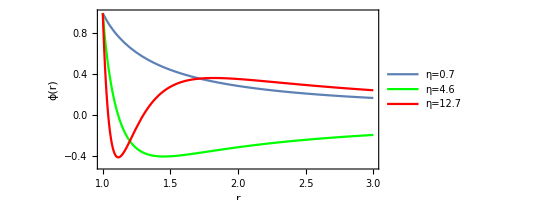

```mathematica
η0=0.7;
η1=4.6;
η2=12.7;
λ0=10^-12;
phih0=0.5092521002504304;
phih1=0.07622939688650629;
phih2=0.006804176641385111;
BCKGRND0=QsGBINT[1,phih0,η0,λ0,10^12,150,ruleQuartic];
BCKGRND1=QsGBINT[1,phih1,η1,λ0,10^12,150,ruleQuartic];
BCKGRND2=QsGBINT[1,phih2,η2,λ0,10^12,150,ruleQuartic];
ϕbck=BCKGRND0[[8]];
ϕbck1=BCKGRND1[[8]];
ϕbck2=BCKGRND2[[8]];
Show[Plot[Legended[ϕbck/phih0,"η=0.7"],{r,1,3},Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium],PlotRange->{-0.5,1}],Plot[Legended[ϕbck1/phih1,"η=4.6"],{r,1,3},PlotRange->{-0.5,1},PlotStyle->Green,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]],Plot[Legended[ϕbck2/phih2,"η=12.7"],{r,1,3},PlotRange->{-0.5,1},PlotStyle->Red,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]]]
```

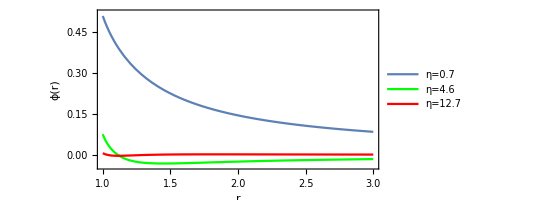

```mathematica
range={-0.04,0.52};
Show[Plot[Legended[ϕbck,"η=0.7"],{r,1,3},Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium],PlotRange->range],Plot[Legended[ϕbck1,"η=4.6"],{r,1,3},PlotRange->range,PlotStyle->Green,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]],Plot[Legended[ϕbck2,"η=12.7"],{r,1,3},PlotRange->range,PlotStyle->Red,Frame->True,AspectRatio->1/2,FrameLabel->{"r","ϕ(r)"},LabelStyle->Directive[Black,Medium]]]
```

$Aborted

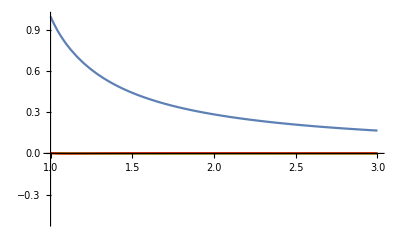

NDSolve::ndode: The equations {(-148498.)[5000000000000001/5000000000000000]==2.22045×10^-16,(-154497.)[5000000000000001/5000000000000000]==2.69345×10^-16} are not differential equations or initial conditions in the dependent variables {ϕ}.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 150 is not a valid variable.

$Aborted

```mathematica
BCKGRND0=QsGBINT[1,phih,η0,λ0,10^12,150,ruleQuartic];
```

```mathematica
Asol=Exp[BCKGRND1[[9]]];
Bsol=Exp[-BCKGRND0[[10]]];
```

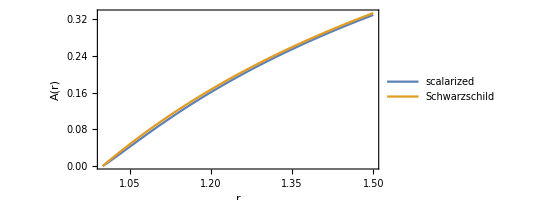

```mathematica
Plot[{Legended[Asol,"scalarized"],Legended[1-1/r,"Schwarzschild"]},{r,1,1.5},Frame->True,AspectRatio->1/2,FrameLabel->{"r","A(r)"},LabelStyle->Directive[Black,Medium]]
```

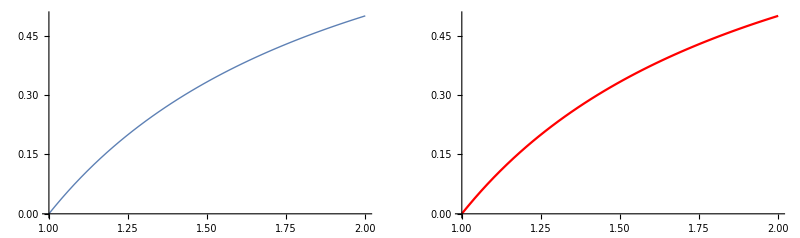

```mathematica
GraphicsRow[{Plot[Asol,{r,1,2},PlotStyle->Thick],Plot[1-1/r,{r,1,2},PlotStyle->Red, PlotStyle->Dotted]}]
```

```mathematica
TortCoord[rr_]:=Integrate[Sqrt[Bsol/Asol],{r,1,rr}]
```

#### Comparing the two sGBINT and the different initial conditions

```mathematica
ClearAll[ϕ,A,B]
```

```mathematica
ϕ[ϵ]
```

ϕ[1/100000]

```mathematica
η0=0.6964;
λ0=10^-12;
phih=0.548048388222048;
(*BCKGRNDfirst=QsGBINT[1,phih,η0,λ0,10^12,150,ruleQuartic];*)
BCKGRNDsecond=sGBINT[1,phih,η0,λ0,10^12,150,ruleQuartic]
```

{1.90022,3.30055×10^-8,1.04762×10^-7,0.416979,2.51457,3.61082×10^-12,0.526256,InterpolatingFunction[…][r],InterpolatingFunction[…][r],0.59832 InterpolatingFunction[…][r],0.59832 InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r]}

```mathematica
{BCKGRNDfirst[[4]],BCKGRNDsecond[[3]]}(*confronto tra le cariche scalari*)
{BCKGRNDfirst[[7]],BCKGRNDsecond[[6]]}(*confronto le masse*)
{BCKGRNDfirst[[3]],BCKGRNDsecond[[2]]}(*confronto i ϕinf*)
```

{0.397458,0.397455}

{0.522782,0.522783}

{0.0000228578,0.000024925}

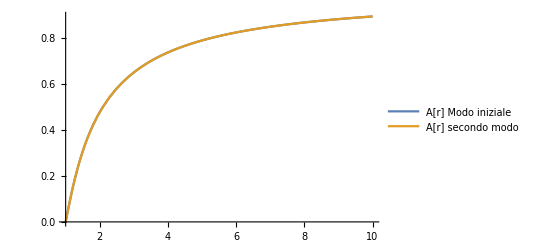

```mathematica
Plot[{Legended[Exp[Υsolshift],"A[r] Modo iniziale"],Legended[Asolshift,"A[r] secondo modo"]},{r,1,10}]
```

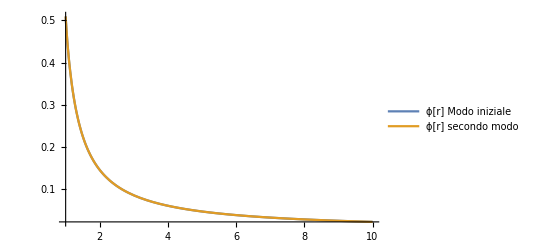

```mathematica
Plot[{Legended[Φsol,"ϕ[r] Modo iniziale"],Legended[ϕsol,"ϕ[r] secondo modo"]},{r,1,10},PlotRange->Full]
```

Dunque se integro usando le boundary conditions uguali a quelle della QsGBINT le soluzioni sono pressoche identiche anche per la sGBINT che usa le equazioni direttamente per A e B e non per Υ e Φ.
Ciò che cambia di più è effettivamente il ϕinf il che può darmi problemi nella ricerca del ϕh per la scalarizzazione

```mathematica
η0=0.7;
λ0=10^-12;
phih=0.5092521002504304;
(*BCKGRNDfirst=QsGBINT[1,phih,η0,λ0,10^12,150,ruleQuartic];*)
BCKGRND2newBCS=sGBINT[1,phih,η0,λ0,10^12,150,ruleQuartic];
```

```mathematica
{BCKGRNDfirst[[4]],BCKGRND2newBCS[[3]]}(*confronto tra le cariche scalari*)
{BCKGRNDfirst[[7]],BCKGRND2newBCS[[6]]}(*confronto le masse*)
{BCKGRNDfirst[[3]],BCKGRND2newBCS[[2]]}(*confronto i ϕinf*)
```

{0.397458,0.39745}

{0.522782,0.522781}

{0.0000228578,0.0000235662}

```mathematica
Plot[{Legended[Exp[Υsolshift],"A[r] Modo iniziale"],Legended[BCKGRND2newBCS[[9]],"A[r] secondo modo"]},{r,1,10}]
```

-Graphics-

```mathematica
Plot[{Legended[Φsol,"ϕ[r] Modo iniziale"],Legended[BCKGRND2newBCS[[7]],"ϕ[r] secondo modo"]},{r,1,10},PlotRange->Full]
```

-Graphics-

Sembra uguale anche per le nuove condizioni al contorno,Ciò che cambia di più è effettivamente il ϕinf il che può darmi problemi nella ricerca del ϕh per la scalarizzazione

### Numerical integration QsGB

Input: 	rh, ϕh, η, λ, rmax, Nh, rule
output:	rh/M, ϕh, ϕinf, Q/M, η/M^2, λ/M^2, M, ϕ[r], Υ[r] , Λ[r]
The integration is not physical unless ϕ_inf=0.

```mathematica
solution=QsGBINT[1,10^-2,0.7,0.0001,10^12,150,ruleQuartic];
ϕinf=solution[[3]]
```

0.000253078

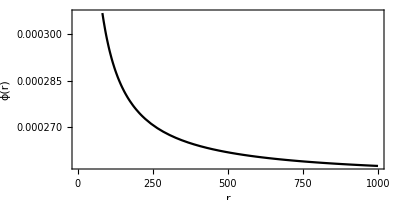

-Graphics-

```mathematica
phisol1=solution[[8]];
gammasol1=solution[[9]];
lambdasol1=solution[[10]];
Plot[phisol1,{r,1.001,10^3},Frame->True,AspectRatio->1/2,
PlotStyle->{Full,Black},
FrameLabel->{"r","ϕ(r)"},Axes-> False]
Plot[{Callout[Exp[gammasol1],"g_tt(r)"],Callout[Exp[lambdasol1],"g_rr(r)"]},{r,1.001,10^3},Frame->True,AspectRatio->1/2,
PlotStyle->{Full,Black},
FrameLabel->{"r",""},Axes-> False]
```

Allora alcune osservazioni: l’integrazione funziona ma sembra che il termine quartico influenzi veramente poco il risultato finale, quasi per nulla. Il campo a r = infinito (rmax) cambia sulla quarta cifra decimale, a η fisso 0.2, per λ dell’ordine di 10^5, ed è il massimo cambiamento che riesco ad avere, oltre non riesco a integrare. Aumentando η riesco ad apprezzare cambiamenti più sostanziali. 
Inoltre non riesco a avere la soluzione con solo termine quartico (ovvero con η=0 , λ != 0) perché ottengo una divergenza 1/0.0.509252
Ora procedo a cercare i range di eta e lambda per cui ho soluzione.

```mathematica
(*Ora dalla condizione di regolarità estraggo il massimo valore di Subscript[Φ, h] per cui ho soluzione. Il minimo è Subscript[Φ, h]=0 in quanto il caso quartico è pari quindi invariante sotto trasformazioni di parità per il campo scalare*)
Findϕhmax[rh0_,η0_,λ0_,MODEL_]:=
(
(*Solve the real/regularity condition*)
ϕhsols=ϕh/.Solve[(1-96 D[ℱ[ϕ[r]],ϕ[r]]^2/(rh)^4/.MODEL/.{ϕ[r]-> ϕh,η-> η0,λ->λ0,rh->rh0})==0,ϕh,Reals];

(*Select the positive value of ϕh. Ci sono sufficienti questi per l'invarianza sotto Φ->-Φ*)
ϕhchosen=Select[ϕhsols,#>0&][[1]]
);
```

```mathematica
Φ4max[η_,λ_]:=Findϕhmax[1,η,λ,ruleQuartic];
Φ4max[dafare[[26]],9.05]
```

Part::partd: Part specification dafare⟦26⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
dafare[[1]]
```

0.723517

#### Graphics

Ricopio input/output della QsGBINT
Input: 	rh, ϕh, η, λ, rmax, Nh, rule
output:	rh/M, ϕh, ϕinf, Q/M, η/M^2, λ/M^2, M, ϕ[r], Υ[r] , Λ[r]

GraphicalPhi:   η/rh^2  ->  Table with 20 columns with  ϕh running between ϕh_min=0+ϵ and ϕh_max found with Findϕh. 
                                   The columns are the dimensionless quantities:  (1/M, ϕh, ϕinf, Q/M, η/M^2,λ/M^2,M, ϕ[r],Υ[r],Λ[r]) .

```mathematica
GraphicalPhi[η_,λ_,nsteps_]:=
(
Φhmax=Φ4max[η, λ];
Φhmin= Φhmax/100000;
TempTab={};
Print[(Φhmax-Φhmin) /nsteps]
(*spazio un range di phi compreso tra Φmax e Φmin*)
Monitor[Do[
Φhi=Φhmin+(Φhmax-Φhmin)ii /nsteps;
result=Join[{Φhi},QsGBINT[1,Φhi,η,λ,10^8,150,ruleQuartic]];
AppendTo[TempTab,result],
{ii,0,nsteps}],N[ii]];
TempTab
);
```

```mathematica
TABa=GraphicalPhi[.69,0,20];
TABb=GraphicalPhi[.7,0,20];
TABc=GraphicalPhi[.71,0,20];
TABd=GraphicalPhi[.72,0,20];
TABe=GraphicalPhi[.73,0,20];
```

0.0295829

0.0291603

0.0287496

0.0283503

0.0279619

```mathematica
(*Table[TABa[[i,10]],{i,20}];*)
```

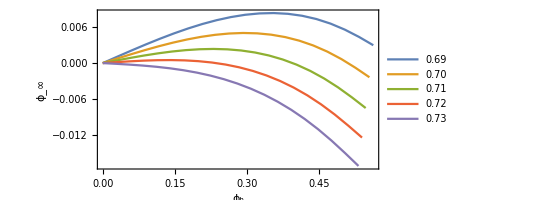

```mathematica
ListLinePlot[{Legended[Table[{TABa[[i,1]],TABa[[i,3]]},{i,20}],"0.69"],Legended[Table[{TABb[[i,1]],TABb[[i,3]]},{i,20}],"0.70"],Legended[Table[{TABc[[i,1]],TABc[[i,3]]},{i,20}],"0.71"],Legended[Table[{TABd[[i,1]],TABd[[i,3]]},{i,20}],"0.72"],Legended[Table[{TABe[[i,1]],TABe[[i,3]]},{i,20}],"0.73"]},Frame->True,AspectRatio->1/2,FrameLabel->{Subscript[ϕ, h],Subscript[ϕ, ∞]},LabelStyle->Directive[Black,Medium]]
```

Plots   ϕinf vs . ϕh .  The only input is η and λ, which now is fixed at 0, in order to compare the solution withe the pure quadratic coupling.  
A non - trivial zero of the function corresponds to a scalarized BH

Problema -> Non riesco a trovare il max phi per λ!=0, quindi vediamo di trovare come fare. 
Soluzione ->  bastava imporre che le soluzioni per il max phi fossero reali. 


Provo adesso a vedere soluzioni diverse per fisso η e λ variabile

```mathematica
TABf=GraphicalPhi[.7,1,20];
TABg=GraphicalPhi[.7,10,20];
TABi=GraphicalPhi[.7,0.01,20];
TABl=GraphicalPhi[.7,0.1,20];
TABm = GraphicalPhi[.7,0.001,20];
```

0.0225808

0.0138799

0.0290206

0.027917

0.0291462

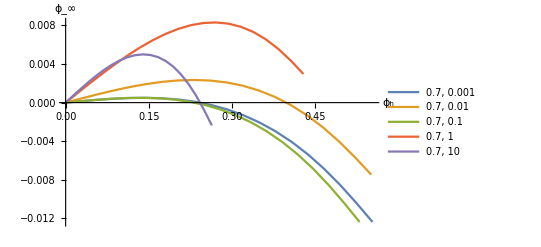

```mathematica
ListLinePlot[{Legended[Table[{TABm[[i,1]],TABd[[i,3]]},{i,20}],"0.7, 0.001"],Legended[Table[{TABi[[i,1]],TABc[[i,3]]},{i,20}],"0.7, 0.01"],Legended[Table[{TABl[[i,1]],TABd[[i,3]]},{i,20}],"0.7, 0.1"],Legended[Table[{TABf[[i,1]],TABa[[i,3]]},{i,20}],"0.7, 1"],Legended[Table[{TABg[[i,1]],TABb[[i,3]]},{i,20}],"0.7, 10"]},AxesLabel->{Subscript[ϕ, h],Subscript[ϕ, ∞]}]
```

Vediamo se il termine quartico riesce a rendere scalarizzabile un eta che prima non lo era

```mathematica
TABn=GraphicalPhi[.69,1,20];
TABp=GraphicalPhi[.69,0.01,20];
TABq=GraphicalPhi[.69,0.1,20];
TABr= GraphicalPhi[.69,0.001,20];
TABs= GraphicalPhi[.69,0,20];
```

0.0227537

0.0294351

0.0282728

0.0295679

0.0295829

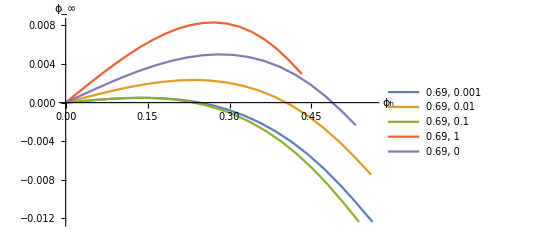

```mathematica
ListLinePlot[{Legended[Table[{TABr[[i,1]],TABd[[i,3]]},{i,20}],"0.69, 0.001"],Legended[Table[{TABp[[i,1]],TABc[[i,3]]},{i,20}],"0.69, 0.01"],Legended[Table[{TABq[[i,1]],TABd[[i,3]]},{i,20}],"0.69, 0.1"],Legended[Table[{TABn[[i,1]],TABa[[i,3]]},{i,20}],"0.69, 1"],Legended[Table[{TABe[[i,1]],TABb[[i,3]]},{i,20}],"0.69, 0"]},AxesLabel->{Subscript[ϕ, h],Subscript[ϕ, ∞]}]
```

```mathematica
(*Non so perché sia con figura sopra a λ fisso a 0 sia sotto con la funzione scal mi viene che la simulazione con η=0.73 λ=0 viene non scalarizzabile, mentre dal grafico sopra sembra di si...*)
```

#### ROOT FINDING

```mathematica
(*Ora dalla condizione di regolarità estraggo il massimo valore di Subscript[Φ, h] per cui ho soluzione. Il minimo è Subscript[Φ, h]=0 in quanto il caso quartico è pari quindi invariante sotto trasformazioni di parità per il campo scalare*)
Findϕhmax[rh0_,η0_,λ0_,MODEL_]:=
(
(*Solve the real/regularity condition*)
ϕhsols=ϕh/.Solve[(1-96 D[ℱ[ϕ[r]],ϕ[r]]^2/(rh)^4/.MODEL/.{ϕ[r]-> ϕh,η-> η0,λ->λ0,rh->rh0})==0,ϕh,Reals];

(*Select the positive value of ϕh. Ci sono sufficienti questi per l'invarianza sotto Φ->-Φ*)
ϕhchosen=Select[ϕhsols,#>0&][[1]]
);
```

```mathematica
Φ4max[η_,λ_]:=Findϕhmax[1,η,λ,ruleQuartic];
eta=1000;
Φ4max[eta,λmultiplier*eta]
```

0.000408248

```mathematica
dafare[[1]]
```

0.723517

Scal:   η/rh^2, λ/rh^2  ->  ϕh   with ϕinf=0.   If for the chosen η there is no scalarization, ϕh=0; if there is scalarization, ϕh is the value corresponding to the scalarized solution, i.e. the one to which corrisponds the non trivial solution with ϕinf=0.
Ricopio input/output della QsGBINT
Input: 	rh, ϕh, η, λ, rmax, Nh, rule
output:	rh/M, ϕh, ϕinf, Q/M, η/M^2, λ/M^2, M, ϕ[r], Υ[r] , Λ[r]

```mathematica
Scal[η0_, λ0_]:=
(
nn=60;
tabϕh=ConstantArray[0,nn];
rh0=1;
NUM=100;
RMAX=10^10;
ϕhmax=N[Findϕhmax[rh0,η0,λ0,ruleQuartic]];
(*Print[ϕhmax];*)
dϕh=ϕhmax/nn;
Do[ϕh1=ii dϕh;
tabϕh[[ii]]=sGBINT[rh0,ϕh1,η0,λ0,RMAX,NUM,ruleQuartic][[3]] ,
{ii,1,nn-2}];
(*Ora devo verificare che esista una soluzione di ϕinf = 0 diversa da quella banale e per farlo guardo se gli estremi di ϕinf sono di segno concorde o no.*)
If[tabϕh[[1]]*tabϕh[[nn-2]]>=0,out=0, Do[If[tabϕh[[ii]]*tabϕh[[ii+1]]<0,out= dϕh(tabϕh[[ii+1]]ii-tabϕh[[ii]](ii+1))/(tabϕh[[ii+1]]-tabϕh[[ii]])],{ii,1,nn-2}]];
out
(*out è in sostanza il punto medio interpolato trale due soluzioni ϕinf con segno discorde*)
);
```

Run over η/rh^2.   For each value, the quantities (  i,  η/rh^2,   η/M^2,   ϕh,   rh/M,   Q/M  ) are printed, while (  η/M^2, λ/M^2 , ϕh,   rh/M,  Q/M  ) are written in table TAB1.
The table (which ca be quite long) is saved as .txt file and as .m file.

the following has been executed, saving the data on tab1.m which will be later loaded; since it is a long run, it has been then commented out; below, to understand how it works, the same run with much less steps

```mathematica
sGBINT[rh0,Findϕhmax[rh0,0.7,0.0001,ruleQuartic]*17/20,0.7,0.0001,RMAX,NUM,ruleQuartic];
```

```mathematica
Scal[0.6964,0.0000000000000001]
```

0.548048

```mathematica
ϕhmax
```

0.571366

```mathematica
(*neta=6000;
TAB1=ConstantArray[0,{neta,neta,5}];
ϵ1=10^(-10);
Do[
{η1=0.2+(i-1) 0.0025,
Do[{
λ1 = 0.0+ 0.01*(j-1),
ϕh1=Scal[η1, λ1],
(*Print[ϕh1]*)
M1=QsGBINT[1,ϕh1+ϵ1,η1,λ1, 10^10,100,ruleQuartic][[7]],
QsuM=QsGBINT[1,ϕh1+ϵ1,η1,λ1, 10^10,100,ruleQuartic][[4]],If[ϕh1>0,Print[j," ",η1," ",λ1," ",η1/M1^2," ",λ1/M1^2," ",ϕh1," " ,1/M1," ",QsuM],Print[i," ",η1]],TAB1[[i,j]]={η1/M1^2,λ1/M1^2,ϕh1,1/M1,QsuM}},{j,1,neta}]},{i,1,neta}];
Export["tab1.txt",TAB1];
Save["tab1.m",TAB1];*)
```

```mathematica
ClearAll[ϕ,A,B,ϕh1];
```

#### Run to obtain the value of ϕh for the fundamental branch for the quadratic case to check in stability_integration.nb if they’re stable or not

```mathematica
ϵ1=10^(-10);
η1=0.725603;
λ1=10^-15;
ϕh1=Scal[η1, λ1];
(*Print[ϕh1]*)
result=sGBINT[1,ϕh1+ϵ1,η1,λ1, 10^10,100,ruleQuartic];
M1=result[[7]];
QsuM=result[[4]];If[ϕh1>0,Print[η1," , "," ",η1/M1^2," , "," ",ϕh1," , " ,1/M1," , ",QsuM],Print[i," ",η1]];
Print[{η1,ϕh1,M1,QsuM}];
Print[{M1/(η1^(1/2)),QsuM*M1/η1^(1/2)}]
```

0.725603 ,  2.90232 ,  0.00954427 , 1.99997 , 0.00852923

{0.725603,0.00954427,0.500008,0.00852923}

{0.586986,0.00500653}

Run to obtain the range of scalarized coupling constant value in the case of quadratic GB gravity (λ=0)

```mathematica
λnull=10^-15;
ηmin=0.6975;
ηmax=0.725;
pts=(ηmax-ηmin)/0.0005;
ϵ1=10^-10;
forStability={};
Monitor[Do[{
ClearAll[ϕ,A,B];
ηtmp=0.0005*(i-1)+ηmin,
ϕhtmp=Scal[ηtmp,λnull],
result=sGBINT[1,ϕhtmp+ϵ1,ηtmp,λnull, 10^10,100,ruleQuartic],
M1=result[[7]],
QsuM=result[[4]],

AppendTo[forStability,{ηtmp,ϕhtmp,M1,QsuM}]},{i,1,pts}],i]
```

```mathematica
Save["../Stability/Data/toCheckStability_FundBranch.m",forStability]
```

The values of the ϕh found are slightly different from the one given by Georgios for the same η: they are underestimated of about a factor 5 on the forth decimal.

============================================================================================================================================================================================
Run for case of Quartic coupling. We select values of λ such that its ratio with η is equal to 0.5, 1, 1.5, 2 as in Silva-Gualtieri  et al. paper

```mathematica
λmultiplier=-1.5;
ηmin=2;
ηmax=3;
divided=0.00005;
pts=(ηmax-ηmin)/divided
ϵ1=10^-10;
quarticBranch={};
Monitor[Do[{
ClearAll[ϕ,A,B],
ηtmp=divided*(i-1)+ηmin,
λtmp=λmultiplier*ηtmp,
ϕhtmp=Scal[ηtmp,λtmp],
If[ϕhtmp!=0,
result=QsGBINT[1,ϕhtmp,ηtmp,λtmp, 10^10,100,ruleQuartic],result={0,0,0,0,0,0,0}],
M1=result[[7]],
QsuM=result[[4]],
AppendTo[quarticBranch,{ηtmp,λtmp,ϕhtmp,M1,QsuM}]},{i,1,pts}],i]
```

20000.

$Aborted

```mathematica
quarticBranch
```

{{2.,-3.,0,0,0}}

```mathematica
quarticBranch
```

{{0.6,-0.3,0,0,0}}

```mathematica
nomefile=StringJoin[{"Data/etaFund_lambda=1η.dat"}];
Save[nomefile,quarticBranch]
```

```mathematica
Save["../toCheckStability_FundBranch.m",forStability]
```

```mathematica
neta=6000;
TAB1=ConstantArray[0,{neta,4,5}];
ϵ1=10^(-10);
Do[
{η1=0.2+(i-1) 0.0025,
Do[{
λ1 = η1*((j-1)*0.5+0.5),
ϕh1=Scal[η1, λ1],
(*Print[ϕh1]*)
result=QsGBINT[1,ϕh1+ϵ1,η1,λ1, 10^10,100,ruleQuartic],
M1=result[[7]],
QsuM=result[[4]],If[ϕh1>0,Print[j," ",η1," ",λ1," ",η1/M1^2," ",λ1/M1^2," ",ϕh1," " ,1/M1," ",QsuM],Print[i," ",η1]],TAB1[[i,j]]={η1/M1^2,λ1/M1^2,ϕh1,1/M1,QsuM}},{j,1,4}]},{i,4700,5020}];
Export["tab1_new4.txt",TAB1];
Save["tab1_new4.m",TAB1];
```

4701 11.95

4701 11.95

4701 11.95

«1 more identical outputs»

4702 11.9525

4702 11.9525

4702 11.9525

«1 more identical outputs»

4703 11.955

4703 11.955

4703 11.955

«1 more identical outputs»

4704 11.9575

4704 11.9575

4704 11.9575

«1 more identical outputs»

4705 11.96

4705 11.96

4705 11.96

«1 more identical outputs»

4706 11.9625

4706 11.9625

4706 11.9625

«1 more identical outputs»

4707 11.965

4707 11.965

4707 11.965

«1 more identical outputs»

4708 11.9675

4708 11.9675

4708 11.9675

«1 more identical outputs»

4709 11.97

4709 11.97

4709 11.97

«1 more identical outputs»

4710 11.9725

4710 11.9725

4710 11.9725

«1 more identical outputs»

4711 11.975

4711 11.975

4711 11.975

«1 more identical outputs»

4712 11.9775

4712 11.9775

4712 11.9775

«1 more identical outputs»

4713 11.98

4713 11.98

4713 11.98

«1 more identical outputs»

4714 11.9825

4714 11.9825

4714 11.9825

«1 more identical outputs»

4715 11.985

4715 11.985

4715 11.985

«1 more identical outputs»

4716 11.9875

4716 11.9875

4716 11.9875

«1 more identical outputs»

4717 11.99

4717 11.99

4717 11.99

«1 more identical outputs»

4718 11.9925

4718 11.9925

4718 11.9925

«1 more identical outputs»

4719 11.995

4719 11.995

4719 11.995

«1 more identical outputs»

4720 11.9975

4720 11.9975

4720 11.9975

«1 more identical outputs»

4721 12.

4721 12.

4721 12.

«1 more identical outputs»

4722 12.0025

4722 12.0025

4722 12.0025

«1 more identical outputs»

4723 12.005

4723 12.005

4723 12.005

«1 more identical outputs»

4724 12.0075

4724 12.0075

4724 12.0075

«1 more identical outputs»

4725 12.01

4725 12.01

4725 12.01

«1 more identical outputs»

4726 12.0125

4726 12.0125

4726 12.0125

«1 more identical outputs»

4727 12.015

4727 12.015

4727 12.015

«1 more identical outputs»

4728 12.0175

4728 12.0175

4728 12.0175

«1 more identical outputs»

4729 12.02

4729 12.02

4729 12.02

«1 more identical outputs»

4730 12.0225

4730 12.0225

4730 12.0225

«1 more identical outputs»

4731 12.025

4731 12.025

4731 12.025

«1 more identical outputs»

4732 12.0275

4732 12.0275

4732 12.0275

«1 more identical outputs»

4733 12.03

4733 12.03

4733 12.03

«1 more identical outputs»

4734 12.0325

4734 12.0325

4734 12.0325

«1 more identical outputs»

4735 12.035

4735 12.035

4735 12.035

«1 more identical outputs»

4736 12.0375

4736 12.0375

4736 12.0375

«1 more identical outputs»

4737 12.04

4737 12.04

4737 12.04

«1 more identical outputs»

4738 12.0425

4738 12.0425

4738 12.0425

«1 more identical outputs»

4739 12.045

4739 12.045

4739 12.045

«1 more identical outputs»

4740 12.0475

2 12.0475 12.0475 47.8905 47.8905 0.0321524 1.99377 0.0335091

3 12.0475 18.0713 47.8911 71.8367 0.0321125 1.99379 0.0334805

4 12.0475 24.095 47.8918 95.7836 0.0320727 1.9938 0.0334519

1 12.05 6.025 47.901 23.9505 0.0321231 1.99379 0.0335015

2 12.05 12.05 47.9016 47.9016 0.0320831 1.9938 0.0334728

3 12.05 18.075 47.9023 71.8534 0.0320433 1.99381 0.0334441

4 12.05 24.1 47.9029 95.8059 0.0320037 1.99383 0.0334155

1 12.0525 6.02625 47.9121 23.9561 0.0320537 1.99381 0.0334649

2 12.0525 12.0525 47.9128 47.9128 0.0320139 1.99383 0.0334361

3 12.0525 18.0788 47.9134 71.8702 0.0319743 1.99384 0.0334074

4 12.0525 24.105 47.9141 95.8282 0.0319349 1.99385 0.0333788

1 12.055 6.0275 47.9233 23.9616 0.0319846 1.99384 0.033428

2 12.055 12.055 47.9239 47.9239 0.0319449 1.99385 0.0333991

3 12.055 18.0825 47.9246 71.8869 0.0319055 1.99386 0.0333704

4 12.055 24.11 47.9252 95.8505 0.0318663 1.99388 0.0333417

1 12.0575 6.02875 47.9344 23.9672 0.0319156 1.99386 0.0333907

2 12.0575 12.0575 47.9351 47.9351 0.0318761 1.99388 0.0333619

3 12.0575 18.0863 47.9357 71.9036 0.0318369 1.99389 0.0333331

4 12.0575 24.115 47.9364 95.8728 0.0317978 1.9939 0.0333044

1 12.06 6.03 47.9456 23.9728 0.0318467 1.99389 0.0333532

2 12.06 12.06 47.9462 47.9462 0.0318075 1.9939 0.0333243

3 12.06 18.09 47.9469 71.9203 0.0317684 1.99391 0.0332955

4 12.06 24.12 47.9475 95.895 0.0317295 1.99393 0.0332668

1 12.0625 6.03125 47.9567 23.9784 0.0317781 1.99391 0.0333154

2 12.0625 12.0625 47.9574 47.9574 0.031739 1.99393 0.0332865

3 12.0625 18.0938 47.958 71.937 0.0317001 1.99394 0.0332577

4 12.0625 24.125 47.9586 95.9173 0.0316614 1.99395 0.0332289

1 12.065 6.0325 47.9679 23.9839 0.0317096 1.99394 0.0332773

2 12.065 12.065 47.9685 47.9685 0.0316707 1.99395 0.0332484

3 12.065 18.0975 47.9691 71.9537 0.0316319 1.99396 0.0332196

4 12.065 24.13 47.9698 95.9396 0.0315934 1.99398 0.0331908

1 12.0675 6.03375 47.979 23.9895 0.0316412 1.99396 0.033239

2 12.0675 12.0675 47.9796 47.9796 0.0316025 1.99398 0.0332101

3 12.0675 18.1013 47.9803 71.9704 0.0315639 1.99399 0.0331812

4 12.0675 24.135 47.9809 95.9618 0.0315256 1.994 0.0331525

1 12.07 6.035 47.9901 23.9951 0.0315731 1.99399 0.0332004

2 12.07 12.07 47.9908 47.9908 0.0315345 1.994 0.0331715

3 12.07 18.105 47.9914 71.9871 0.0314961 1.99401 0.0331426

4 12.07 24.14 47.992 95.984 0.0314579 1.99403 0.0331139

1 12.0725 6.03625 48.0013 24.0006 0.0315051 1.99401 0.0331616

2 12.0725 12.0725 48.0019 48.0019 0.0314667 1.99402 0.0331327

3 12.0725 18.1088 48.0025 72.0038 0.0314285 1.99404 0.0331038

4 12.0725 24.145 48.0031 96.0063 0.0313904 1.99405 0.0330751

1 12.075 6.0375 48.0124 24.0062 0.0314372 1.99404 0.0331226

2 12.075 12.075 48.013 48.013 0.031399 1.99405 0.0330937

3 12.075 18.1125 48.0136 72.0204 0.031361 1.99406 0.0330648

4 12.075 24.15 48.0142 96.0285 0.0313231 1.99407 0.0330361

1 12.0775 6.03875 48.0235 24.0117 0.0313696 1.99406 0.0330833

2 12.0775 12.0775 48.0241 48.0241 0.0313315 1.99407 0.0330544

3 12.0775 18.1162 48.0247 72.0371 0.0312937 1.99409 0.0330256

4 12.0775 24.155 48.0253 96.0507 0.031256 1.9941 0.0329968

1 12.08 6.04 48.0346 24.0173 0.0313021 1.99408 0.0330439

2 12.08 12.08 48.0352 48.0352 0.0312642 1.9941 0.033015

3 12.08 18.12 48.0358 72.0537 0.0312265 1.99411 0.0329861

4 12.08 24.16 48.0364 96.0729 0.031189 1.99412 0.0329574

1 12.0825 6.04125 48.0457 24.0229 0.0312347 1.99411 0.0330042

2 12.0825 12.0825 48.0463 48.0463 0.031197 1.99412 0.0329753

3 12.0825 18.1238 48.0469 72.0704 0.0311595 1.99413 0.0329465

4 12.0825 24.165 48.0475 96.0951 0.0311221 1.99415 0.0329178

1 12.085 6.0425 48.0568 24.0284 0.0311675 1.99413 0.0329644

2 12.085 12.085 48.0574 48.0574 0.03113 1.99415 0.0329355

3 12.085 18.1275 48.058 72.087 0.0310926 1.99416 0.0329067

4 12.085 24.17 48.0586 96.1173 0.0310554 1.99417 0.032878

1 12.0875 6.04375 48.0679 24.034 0.0311005 1.99416 0.0329244

2 12.0875 12.0875 48.0685 48.0685 0.0310631 1.99417 0.0328955

3 12.0875 18.1313 48.0691 72.1037 0.031026 1.99418 0.0328667

4 12.0875 24.175 48.0697 96.1394 0.0309889 1.99419 0.032838

1 12.09 6.045 48.079 24.0395 0.0310337 1.99418 0.0328842

2 12.09 12.09 48.0796 48.0796 0.0309965 1.99419 0.0328553

3 12.09 18.135 48.0802 72.1203 0.0309594 1.99421 0.0328266

4 12.09 24.18 48.0808 96.1616 0.0309226 1.99422 0.0327979

1 12.0925 6.04625 48.0901 24.045 0.030967 1.9942 0.0328438

2 12.0925 12.0925 48.0907 48.0907 0.0309299 1.99422 0.032815

3 12.0925 18.1387 48.0913 72.1369 0.0308931 1.99423 0.0327862

4 12.0925 24.185 48.0919 96.1837 0.0308564 1.99424 0.0327576

1 12.095 6.0475 48.1012 24.0506 0.0309004 1.99423 0.0328033

2 12.095 12.095 48.1018 48.1018 0.0308636 1.99424 0.0327745

3 12.095 18.1425 48.1024 72.1535 0.0308268 1.99425 0.0327457

4 12.095 24.19 48.1029 96.2059 0.0307903 1.99427 0.0327171

1 12.0975 6.04875 48.1122 24.0561 0.030834 1.99425 0.0327626

2 12.0975 12.0975 48.1128 48.1128 0.0307973 1.99426 0.0327338

3 12.0975 18.1463 48.1134 72.1701 0.0307608 1.99428 0.0327051

4 12.0975 24.195 48.114 96.228 0.0307244 1.99429 0.0326765

1 12.1 6.05 48.1233 24.0617 0.0307678 1.99428 0.0327218

2 12.1 12.1 48.1239 48.1239 0.0307313 1.99429 0.032693

3 12.1 18.15 48.1245 72.1867 0.0306949 1.9943 0.0326643

4 12.1 24.2 48.1251 96.2501 0.0306587 1.99431 0.0326358

1 12.1025 6.05125 48.1344 24.0672 0.0307018 1.9943 0.0326808

2 12.1025 12.1025 48.135 48.135 0.0306654 1.99431 0.0326521

3 12.1025 18.1538 48.1356 72.2033 0.0306292 1.99432 0.0326234

4 12.1025 24.205 48.1361 96.2723 0.0305931 1.99433 0.0325949

1 12.105 6.0525 48.1455 24.0727 0.0306359 1.99432 0.0326397

2 12.105 12.105 48.146 48.146 0.0305996 1.99433 0.032611

3 12.105 18.1575 48.1466 72.2199 0.0305636 1.99435 0.0325824

4 12.105 24.21 48.1472 96.2944 0.0305277 1.99436 0.0325539

1 12.1075 6.05375 48.1565 24.0783 0.0305701 1.99434 0.0325984

2 12.1075 12.1075 48.1571 48.1571 0.030534 1.99436 0.0325698

3 12.1075 18.1613 48.1577 72.2365 0.0304982 1.99437 0.0325412

4 12.1075 24.215 48.1582 96.3165 0.0304624 1.99438 0.0325127

1 12.11 6.055 48.1676 24.0838 0.0305045 1.99437 0.0325571

2 12.11 12.11 48.1681 48.1681 0.0304686 1.99438 0.0325284

3 12.11 18.165 48.1687 72.2531 0.0304329 1.99439 0.0324999

4 12.11 24.22 48.1693 96.3386 0.0303973 1.9944 0.0324714

1 12.1125 6.05625 48.1786 24.0893 0.0304391 1.99439 0.0325156

2 12.1125 12.1125 48.1792 48.1792 0.0304033 1.9944 0.032487

3 12.1125 18.1688 48.1798 72.2696 0.0303678 1.99441 0.0324585

4 12.1125 24.225 48.1803 96.3607 0.0303324 1.99443 0.0324301

1 12.115 6.0575 48.1897 24.0948 0.0303738 1.99441 0.032474

2 12.115 12.115 48.1902 48.1902 0.0303382 1.99443 0.0324454

3 12.115 18.1725 48.1908 72.2862 0.0303028 1.99444 0.0324169

4 12.115 24.23 48.1914 96.3827 0.0302675 1.99445 0.0323886

1 12.1175 6.05875 48.2007 24.1004 0.0303087 1.99444 0.0324322

2 12.1175 12.1175 48.2013 48.2013 0.0302718 1.99445 0.0324024

3 12.1175 18.1763 48.2019 72.3028 0.0302347 1.99446 0.0323722

4 12.1175 24.235 48.2025 96.405 0.0301978 1.99447 0.0323422

1 12.12 6.06 48.2119 24.1059 0.0302381 1.99446 0.0323852

2 12.12 12.12 48.2124 48.2124 0.030201 1.99447 0.032355

3 12.12 18.18 48.213 72.3196 0.0301641 1.99449 0.0323249

4 12.12 24.24 48.2136 96.4272 0.0301274 1.9945 0.032295

1 12.1225 6.06125 48.223 24.1115 0.0301674 1.99449 0.0323377

2 12.1225 12.1225 48.2236 48.2236 0.0301305 1.9945 0.0323076

3 12.1225 18.1837 48.2242 72.3363 0.0300938 1.99451 0.0322776

4 12.1225 24.245 48.2248 96.4495 0.0300572 1.99452 0.0322476

1 12.125 6.0625 48.2341 24.1171 0.0300969 1.99451 0.0322901

2 12.125 12.125 48.2347 48.2347 0.0300602 1.99452 0.0322601

3 12.125 18.1875 48.2353 72.3529 0.0300237 1.99453 0.0322301

4 12.125 24.25 48.2359 96.4717 0.0299873 1.99455 0.0322003

1 12.1275 6.06375 48.2453 24.1226 0.0300266 1.99454 0.0322425

2 12.1275 12.1275 48.2458 48.2458 0.0299901 1.99455 0.0322125

3 12.1275 18.1913 48.2464 72.3696 0.0299537 1.99456 0.0321826

4 12.1275 24.255 48.247 96.494 0.0299176 1.99457 0.0321528

1 12.13 6.065 48.2564 24.1282 0.0299565 1.99456 0.0321948

2 12.13 12.13 48.257 48.257 0.0299202 1.99457 0.0321648

3 12.13 18.195 48.2575 72.3863 0.029884 1.99458 0.032135

4 12.13 24.26 48.2581 96.5162 0.0298481 1.99459 0.0321053

1 12.1325 6.06625 48.2675 24.1337 0.0298866 1.99458 0.032147

2 12.1325 12.1325 48.2681 48.2681 0.0298505 1.9946 0.0321171

3 12.1325 18.1988 48.2686 72.403 0.0298145 1.99461 0.0320873

4 12.1325 24.265 48.2692 96.5384 0.0297787 1.99462 0.0320577

1 12.135 6.0675 48.2786 24.1393 0.029817 1.99461 0.0320991

2 12.135 12.135 48.2792 48.2792 0.029781 1.99462 0.0320693

3 12.135 18.2025 48.2797 72.4196 0.0297452 1.99463 0.0320396

4 12.135 24.27 48.2803 96.5606 0.0297096 1.99464 0.03201

1 12.1375 6.06875 48.2897 24.1449 0.0297475 1.99463 0.0320512

2 12.1375 12.1375 48.2903 48.2903 0.0297118 1.99464 0.0320215

3 12.1375 18.2062 48.2908 72.4363 0.0296762 1.99465 0.0319919

4 12.1375 24.275 48.2914 96.5828 0.0296407 1.99467 0.0319623

1 12.14 6.07 48.3008 24.1504 0.0296783 1.99466 0.0320033

2 12.14 12.14 48.3014 48.3014 0.0296427 1.99467 0.0319736

3 12.14 18.21 48.3019 72.4529 0.0296073 1.99468 0.031944

4 12.14 24.28 48.3025 96.605 0.0295721 1.99469 0.0319146

1 12.1425 6.07125 48.3119 24.156 0.0296093 1.99468 0.0319553

2 12.1425 12.1425 48.3125 48.3125 0.0295739 1.99469 0.0319257

3 12.1425 18.2138 48.313 72.4695 0.0295386 1.9947 0.0318962

4 12.1425 24.285 48.3136 96.6271 0.0295036 1.99471 0.0318668

1 12.145 6.0725 48.323 24.1615 0.0295404 1.9947 0.0319072

2 12.145 12.145 48.3236 48.3236 0.0295052 1.99471 0.0318777

3 12.145 18.2175 48.3241 72.4862 0.0294702 1.99473 0.0318483

4 12.145 24.29 48.3247 96.6493 0.0294353 1.99474 0.031819

1 12.1475 6.07375 48.3341 24.167 0.0294718 1.99473 0.0318591

2 12.1475 12.1475 48.3346 48.3346 0.0294368 1.99474 0.0318297

3 12.1475 18.2212 48.3352 72.5028 0.0294019 1.99475 0.0318004

4 12.1475 24.295 48.3357 96.6714 0.0293672 1.99476 0.0317711

1 12.15 6.075 48.3452 24.1726 0.0294034 1.99475 0.031811

2 12.15 12.15 48.3457 48.3457 0.0293686 1.99476 0.0317817

3 12.15 18.225 48.3463 72.5194 0.0293339 1.99477 0.0317524

4 12.15 24.3 48.3468 96.6936 0.0292994 1.99478 0.0317233

1 12.1525 6.07625 48.3562 24.1781 0.0293352 1.99477 0.0317629

2 12.1525 12.1525 48.3568 48.3568 0.0293005 1.99478 0.0317336

3 12.1525 18.2287 48.3573 72.536 0.029266 1.9948 0.0317044

4 12.1525 24.305 48.3579 96.7157 0.0292317 1.99481 0.0316753

1 12.155 6.0775 48.3673 24.1837 0.0292672 1.9948 0.0317147

2 12.155 12.155 48.3678 48.3678 0.0292327 1.99481 0.0316855

3 12.155 18.2325 48.3684 72.5526 0.0291984 1.99482 0.0316564

4 12.155 24.31 48.3689 96.7378 0.0291642 1.99483 0.0316274

1 12.1575 6.07875 48.3784 24.1892 0.0291994 1.99482 0.0316665

2 12.1575 12.1575 48.3789 48.3789 0.0291651 1.99483 0.0316374

3 12.1575 18.2363 48.3794 72.5692 0.029131 1.99484 0.0316083

4 12.1575 24.315 48.38 96.7599 0.029097 1.99485 0.0315794

1 12.16 6.08 48.3894 24.1947 0.0291318 1.99484 0.0316183

2 12.16 12.16 48.39 48.39 0.0290977 1.99485 0.0315892

3 12.16 18.24 48.3905 72.5857 0.0290637 1.99486 0.0315603

4 12.16 24.32 48.391 96.782 0.0290299 1.99487 0.0315315

1 12.1625 6.08125 48.4005 24.2002 0.0290644 1.99486 0.0315701

2 12.1625 12.1625 48.401 48.401 0.0290305 1.99488 0.0315411

3 12.1625 18.2438 48.4015 72.6023 0.0289967 1.99489 0.0315122

4 12.1625 24.325 48.4021 96.8041 0.028963 1.9949 0.0314835

1 12.165 6.0825 48.4115 24.2058 0.0289972 1.99489 0.0315218

2 12.165 12.165 48.412 48.412 0.0289635 1.9949 0.0314929

3 12.165 18.2475 48.4126 72.6189 0.0289298 1.99491 0.0314641

4 12.165 24.33 48.4131 96.8262 0.0288964 1.99492 0.0314355

1 12.1675 6.08375 48.4226 24.2113 0.0289302 1.99491 0.0314736

2 12.1675 12.1675 48.4231 48.4231 0.0288966 1.99492 0.0314447

3 12.1675 18.2513 48.4236 72.6354 0.0288632 1.99493 0.0314161

4 12.1675 24.335 48.4241 96.8482 0.0288299 1.99494 0.0313875

1 12.17 6.085 48.4336 24.2168 0.0288635 1.99493 0.0314253

2 12.17 12.17 48.4341 48.4341 0.02883 1.99494 0.0313966

3 12.17 18.255 48.4346 72.652 0.0287967 1.99495 0.031368

4 12.17 24.34 48.4351 96.8703 0.0287636 1.99496 0.0313395

1 12.1725 6.08625 48.4446 24.2223 0.0287969 1.99495 0.031377

2 12.1725 12.1725 48.4452 48.4452 0.0287636 1.99496 0.0313484

3 12.1725 18.2588 48.4457 72.6685 0.0287305 1.99498 0.0313199

4 12.1725 24.345 48.4462 96.8923 0.0286975 1.99499 0.0312915

1 12.175 6.0875 48.4557 24.2278 0.0287305 1.99498 0.0313288

2 12.175 12.175 48.4562 48.4562 0.0286974 1.99499 0.0313002

3 12.175 18.2625 48.4567 72.685 0.0286644 1.995 0.0312718

4 12.175 24.35 48.4572 96.9144 0.0286316 1.99501 0.0312434

1 12.1775 6.08875 48.4667 24.2333 0.0286643 1.995 0.0312805

2 12.1775 12.1775 48.4672 48.4672 0.0286313 1.99501 0.031252

3 12.1775 18.2663 48.4677 72.7015 0.0285986 1.99502 0.0312237

4 12.1775 24.355 48.4682 96.9364 0.0285659 1.99503 0.0311954

1 12.18 6.09 48.4777 24.2389 0.0285982 1.99502 0.0312322

2 12.18 12.18 48.4782 48.4782 0.0285655 1.99503 0.0312038

3 12.18 18.27 48.4787 72.7181 0.0285329 1.99504 0.0311756

4 12.18 24.36 48.4792 96.9584 0.0285004 1.99505 0.0311474

1 12.1825 6.09125 48.4887 24.2444 0.0285324 1.99504 0.031184

2 12.1825 12.1825 48.4892 48.4892 0.0284998 1.99505 0.0311557

3 12.1825 18.2738 48.4897 72.7346 0.0284674 1.99506 0.0311275

4 12.1825 24.365 48.4902 96.9804 0.0284351 1.99507 0.0310994

1 12.185 6.0925 48.4997 24.2499 0.0284668 1.99506 0.0311357

2 12.185 12.185 48.5002 48.5002 0.0284326 1.99507 0.0311057

3 12.185 18.2775 48.5008 72.7512 0.028398 1.99509 0.0310752

4 12.185 24.37 48.5013 97.0026 0.0283635 1.9951 0.0310448

1 12.1875 6.09375 48.5109 24.2554 0.0283934 1.99509 0.0310793

2 12.1875 12.1875 48.5114 48.5114 0.0283587 1.9951 0.0310488

3 12.1875 18.2813 48.5119 72.7679 0.0283243 1.99511 0.0310184

4 12.1875 24.375 48.5124 97.0249 0.02829 1.99512 0.0309881

1 12.19 6.095 48.522 24.261 0.0283196 1.99511 0.0310223

2 12.19 12.19 48.5225 48.5225 0.0282852 1.99512 0.0309919

3 12.19 18.285 48.5231 72.7846 0.0282509 1.99513 0.0309616

4 12.19 24.38 48.5236 97.0472 0.0282169 1.99515 0.0309315

1 12.1925 6.09625 48.5331 24.2666 0.028246 1.99514 0.0309654

2 12.1925 12.1925 48.5337 48.5337 0.0282119 1.99515 0.0309351

3 12.1925 18.2888 48.5342 72.8013 0.0281778 1.99516 0.030905

4 12.1925 24.385 48.5347 97.0694 0.0281439 1.99517 0.0308749

1 12.195 6.0975 48.5443 24.2721 0.0281728 1.99516 0.0309086

2 12.195 12.195 48.5448 48.5448 0.0281388 1.99517 0.0308784

3 12.195 18.2925 48.5453 72.818 0.028105 1.99518 0.0308483

4 12.195 24.39 48.5458 97.0916 0.0280713 1.99519 0.0308184

1 12.1975 6.09875 48.5554 24.2777 0.0280998 1.99519 0.0308518

2 12.1975 12.1975 48.5559 48.5559 0.028066 1.9952 0.0308217

3 12.1975 18.2963 48.5564 72.8346 0.0280324 1.99521 0.0307918

4 12.1975 24.395 48.5569 97.1138 0.0279989 1.99522 0.030762

1 12.2 6.1 48.5665 24.2832 0.0280271 1.99521 0.0307951

2 12.2 12.2 48.567 48.567 0.0279935 1.99522 0.0307651

3 12.2 18.3 48.5675 72.8513 0.0279601 1.99523 0.0307353

4 12.2 24.4 48.568 97.1361 0.0279268 1.99524 0.0307056

1 12.2025 6.10125 48.5776 24.2888 0.0279547 1.99523 0.0307384

2 12.2025 12.2025 48.5781 48.5781 0.0279213 1.99524 0.0307086

3 12.2025 18.3037 48.5786 72.8679 0.0278881 1.99525 0.0306789

4 12.2025 24.405 48.5791 97.1582 0.027855 1.99526 0.0306493

1 12.205 6.1025 48.5887 24.2944 0.0278825 1.99526 0.0306818

2 12.205 12.205 48.5892 48.5892 0.0278493 1.99527 0.0306521

3 12.205 18.3075 48.5897 72.8846 0.0278163 1.99528 0.0306225

4 12.205 24.41 48.5902 97.1804 0.0277834 1.99529 0.0305931

1 12.2075 6.10375 48.5998 24.2999 0.0278106 1.99528 0.0306253

2 12.2075 12.2075 48.6003 48.6003 0.0277776 1.99529 0.0305957

3 12.2075 18.3113 48.6008 72.9012 0.0277448 1.9953 0.0305663

4 12.2075 24.415 48.6013 97.2026 0.0277121 1.99531 0.0305369

1 12.21 6.105 48.6109 24.3054 0.027739 1.9953 0.0305689

2 12.21 12.21 48.6114 48.6114 0.0277062 1.99531 0.0305394

3 12.21 18.315 48.6119 72.9178 0.0276735 1.99532 0.0305101

4 12.21 24.42 48.6124 97.2247 0.0276411 1.99533 0.0304809

1 12.2125 6.10625 48.622 24.311 0.0276676 1.99533 0.0305125

2 12.2125 12.2125 48.6225 48.6225 0.027635 1.99534 0.0304832

3 12.2125 18.3188 48.623 72.9344 0.0276026 1.99535 0.030454

4 12.2125 24.425 48.6234 97.2469 0.0275703 1.99536 0.0304249

1 12.215 6.1075 48.633 24.3165 0.0275965 1.99535 0.0304563

2 12.215 12.215 48.6335 48.6335 0.0275641 1.99536 0.0304271

3 12.215 18.3225 48.634 72.951 0.0275318 1.99537 0.030398

4 12.215 24.43 48.6345 97.269 0.0274997 1.99538 0.030369

1 12.2175 6.10875 48.6441 24.3221 0.0275256 1.99537 0.0304001

2 12.2175 12.2175 48.6446 48.6446 0.0274934 1.99538 0.030371

3 12.2175 18.3262 48.6451 72.9676 0.0274613 1.99539 0.030342

4 12.2175 24.435 48.6456 97.2911 0.0274294 1.9954 0.0303131

1 12.22 6.11 48.6552 24.3276 0.027455 1.9954 0.030344

2 12.22 12.22 48.6557 48.6557 0.027423 1.99541 0.030315

3 12.22 18.33 48.6561 72.9842 0.0273911 1.99541 0.0302862

4 12.22 24.44 48.6566 97.3132 0.0273594 1.99542 0.0302574

1 12.2225 6.11125 48.6662 24.3331 0.0273847 1.99542 0.030288

2 12.2225 12.2225 48.6667 48.6667 0.0273528 1.99543 0.0302591

3 12.2225 18.3338 48.6672 73.0008 0.0273212 1.99544 0.0302304

4 12.2225 24.445 48.6677 97.3353 0.0272896 1.99545 0.0302018

1 12.225 6.1125 48.6773 24.3386 0.0273146 1.99544 0.0302321

2 12.225 12.225 48.6778 48.6778 0.0272829 1.99545 0.0302033

3 12.225 18.3375 48.6782 73.0173 0.0272514 1.99546 0.0301747

4 12.225 24.45 48.6787 97.3574 0.0272201 1.99547 0.0301462

1 12.2275 6.11375 48.6883 24.3442 0.0272447 1.99546 0.0301762

2 12.2275 12.2275 48.6888 48.6888 0.0272133 1.99547 0.0301476

3 12.2275 18.3413 48.6893 73.0339 0.027182 1.99548 0.0301191

4 12.2275 24.455 48.6897 97.3795 0.0271508 1.99549 0.0300907

1 12.23 6.115 48.6994 24.3497 0.0271751 1.99548 0.0301205

2 12.23 12.23 48.6998 48.6998 0.0271439 1.99549 0.030092

3 12.23 18.345 48.7003 73.0504 0.0271128 1.9955 0.0300636

4 12.23 24.46 48.7008 97.4015 0.0270818 1.99551 0.0300354

1 12.2325 6.11625 48.7104 24.3552 0.0271058 1.99551 0.0300649

2 12.2325 12.2325 48.7109 48.7109 0.0270747 1.99552 0.0300365

3 12.2325 18.3488 48.7113 73.067 0.0270438 1.99553 0.0300082

4 12.2325 24.465 48.7118 97.4236 0.027013 1.99554 0.0299801

1 12.235 6.1175 48.7214 24.3607 0.0270367 1.99553 0.0300093

2 12.235 12.235 48.7219 48.7219 0.0270058 1.99554 0.0299811

3 12.235 18.3525 48.7223 73.0835 0.0269751 1.99555 0.0299529

4 12.235 24.47 48.7228 97.4456 0.0269445 1.99556 0.0299249

1 12.2375 6.11875 48.7324 24.3662 0.0269679 1.99555 0.0299539

2 12.2375 12.2375 48.7329 48.7329 0.0269372 1.99556 0.0299257

3 12.2375 18.3563 48.7334 73.1 0.0269066 1.99557 0.0298977

4 12.2375 24.475 48.7338 97.4676 0.0268762 1.99558 0.0298698

1 12.24 6.12 48.7435 24.3717 0.0268993 1.99557 0.0298985

2 12.24 12.24 48.7439 48.7439 0.0268688 1.99558 0.0298705

3 12.24 18.36 48.7444 73.1165 0.0268384 1.99559 0.0298426

4 12.24 24.48 48.7448 97.4896 0.0268081 1.9956 0.0298148

1 12.2425 6.12125 48.7545 24.3772 0.0268309 1.99559 0.0298433

2 12.2425 12.2425 48.7549 48.7549 0.0268006 1.9956 0.0298154

3 12.2425 18.3638 48.7554 73.133 0.0267704 1.99561 0.0297876

4 12.2425 24.485 48.7558 97.5116 0.0267403 1.99562 0.0297599

1 12.245 6.1225 48.7655 24.3827 0.0267628 1.99562 0.0297881

2 12.245 12.245 48.7659 48.7659 0.0267327 1.99562 0.0297603

3 12.245 18.3675 48.7664 73.1495 0.0267026 1.99563 0.0297327

4 12.245 24.49 48.7668 97.5336 0.0266727 1.99564 0.0297051

1 12.2475 6.12375 48.7765 24.3882 0.026695 1.99564 0.0297331

2 12.2475 12.2475 48.7769 48.7769 0.026665 1.99565 0.0297054

3 12.2475 18.3712 48.7773 73.166 0.0266351 1.99565 0.0296779

4 12.2475 24.495 48.7778 97.5556 0.026605 1.99566 0.02965

1 12.25 6.125 48.7875 24.3938 0.026624 1.99566 0.0296746

2 12.25 12.25 48.788 48.788 0.0265916 1.99567 0.0296442

3 12.25 18.375 48.7885 73.1827 0.0265594 1.99568 0.029614

4 12.25 24.5 48.7889 97.5779 0.0265272 1.99569 0.029584

1 12.2525 6.12625 48.7987 24.3993 0.026546 1.99568 0.0296082

2 12.2525 12.2525 48.7991 48.7991 0.0265138 1.99569 0.0295781

3 12.2525 18.3788 48.7996 73.1994 0.0264817 1.9957 0.029548

4 12.2525 24.505 48.8001 97.6002 0.0264498 1.99571 0.0295181

1 12.255 6.1275 48.8098 24.4049 0.0264683 1.99571 0.0295421

2 12.255 12.255 48.8103 48.8103 0.0264363 1.99572 0.0295121

3 12.255 18.3825 48.8108 73.2161 0.0264045 1.99573 0.0294822

4 12.255 24.51 48.8112 97.6224 0.0263728 1.99574 0.0294524

1 12.2575 6.12875 48.821 24.4105 0.0263909 1.99573 0.0294761

2 12.2575 12.2575 48.8214 48.8214 0.0263591 1.99574 0.0294462

3 12.2575 18.3863 48.8219 73.2328 0.0263275 1.99575 0.0294165

4 12.2575 24.515 48.8223 97.6447 0.0262961 1.99576 0.0293869

1 12.26 6.13 48.8321 24.416 0.0263139 1.99576 0.0294103

2 12.26 12.26 48.8326 48.8326 0.0262823 1.99577 0.0293806

3 12.26 18.39 48.833 73.2495 0.0262509 1.99577 0.029351

4 12.26 24.52 48.8335 97.6669 0.0262197 1.99578 0.0293216

1 12.2625 6.13125 48.8432 24.4216 0.0262372 1.99578 0.0293447

2 12.2625 12.2625 48.8437 48.8437 0.0262059 1.99579 0.0293152

3 12.2625 18.3937 48.8441 73.2662 0.0261747 1.9958 0.0292858

4 12.2625 24.525 48.8446 97.6892 0.0261437 1.99581 0.0292565

1 12.265 6.1325 48.8543 24.4272 0.0261608 1.9958 0.0292793

2 12.265 12.265 48.8548 48.8548 0.0261297 1.99581 0.0292499

3 12.265 18.3975 48.8552 73.2828 0.0260988 1.99582 0.0292207

4 12.265 24.53 48.8557 97.7114 0.026068 1.99583 0.0291915

1 12.2675 6.13375 48.8654 24.4327 0.0260848 1.99583 0.0292141

2 12.2675 12.2675 48.8659 48.8659 0.0260539 1.99584 0.0291849

3 12.2675 18.4013 48.8663 73.2995 0.0260232 1.99585 0.0291558

4 12.2675 24.535 48.8668 97.7335 0.0259926 1.99585 0.0291268

1 12.27 6.135 48.8765 24.4383 0.0260092 1.99585 0.0291491

2 12.27 12.27 48.877 48.877 0.0259785 1.99586 0.02912

3 12.27 18.405 48.8774 73.3161 0.0259479 1.99587 0.0290911

4 12.27 24.54 48.8779 97.7557 0.0259176 1.99588 0.0290622

1 12.2725 6.13625 48.8876 24.4438 0.0259338 1.99587 0.0290842

2 12.2725 12.2725 48.8881 48.8881 0.0259033 1.99588 0.0290553

3 12.2725 18.4087 48.8885 73.3328 0.025873 1.99589 0.0290265

4 12.2725 24.545 48.8889 97.7779 0.0258428 1.9959 0.0289979

1 12.275 6.1375 48.8987 24.4494 0.0258588 1.9959 0.0290196

2 12.275 12.275 48.8992 48.8992 0.0258285 1.99591 0.0289908

3 12.275 18.4125 48.8996 73.3494 0.0257984 1.99591 0.0289622

4 12.275 24.55 48.9 97.8 0.0257685 1.99592 0.0289337

1 12.2775 6.13875 48.9098 24.4549 0.0257841 1.99592 0.0289551

2 12.2775 12.2775 48.9102 48.9102 0.0257541 1.99593 0.0289265

3 12.2775 18.4162 48.9107 73.366 0.0257242 1.99594 0.0288981

4 12.2775 24.555 48.9111 97.8222 0.0256944 1.99595 0.0288697

1 12.28 6.14 48.9209 24.4604 0.0257098 1.99594 0.0288909

2 12.28 12.28 48.9213 48.9213 0.0256799 1.99595 0.0288624

3 12.28 18.42 48.9217 73.3826 0.0256502 1.99596 0.0288341

4 12.28 24.56 48.9221 97.8443 0.0256207 1.99597 0.0288059

1 12.2825 6.14125 48.9319 24.466 0.0256357 1.99596 0.0288268

2 12.2825 12.2825 48.9323 48.9323 0.0256061 1.99597 0.0287985

3 12.2825 18.4238 48.9328 73.3992 0.0255766 1.99598 0.0287704

4 12.2825 24.565 48.9332 97.8664 0.0255472 1.99599 0.0287423

1 12.285 6.1425 48.943 24.4715 0.025562 1.99599 0.028763

2 12.285 12.285 48.9434 48.9434 0.0255326 1.996 0.0287348

3 12.285 18.4275 48.9438 73.4157 0.0255033 1.996 0.0287068

4 12.285 24.57 48.9442 97.8885 0.0254741 1.99601 0.0286789

1 12.2875 6.14375 48.954 24.477 0.0254886 1.99601 0.0286993

2 12.2875 12.2875 48.9544 48.9544 0.0254594 1.99602 0.0286713

3 12.2875 18.4313 48.9549 73.4323 0.0254303 1.99603 0.0286435

4 12.2875 24.575 48.9553 97.9105 0.0254013 1.99603 0.0286157

1 12.29 6.145 48.9651 24.4825 0.0254156 1.99603 0.0286358

2 12.29 12.29 48.9655 48.9655 0.0253865 1.99604 0.028608

3 12.29 18.435 48.9659 73.4488 0.0253576 1.99605 0.0285803

4 12.29 24.58 48.9663 97.9326 0.0253289 1.99606 0.0285527

1 12.2925 6.14625 48.9761 24.4881 0.0253428 1.99605 0.0285725

2 12.2925 12.2925 48.9765 48.9765 0.025314 1.99606 0.0285449

3 12.2925 18.4388 48.9769 73.4654 0.0252853 1.99607 0.0285173

4 12.2925 24.585 48.9773 97.9546 0.0252567 1.99608 0.0284899

1 12.295 6.1475 48.9871 24.4936 0.0252704 1.99607 0.0285095

2 12.295 12.295 48.9875 48.9875 0.0252417 1.99608 0.0284819

3 12.295 18.4425 48.9879 73.4819 0.0252132 1.99609 0.0284546

4 12.295 24.59 48.9883 97.9767 0.0251848 1.9961 0.0284273

1 12.2975 6.14875 48.9981 24.4991 0.0251982 1.9961 0.0284466

2 12.2975 12.2975 48.9985 48.9985 0.0251698 1.9961 0.0284192

3 12.2975 18.4463 48.9989 73.4984 0.0251415 1.99611 0.028392

4 12.2975 24.595 48.9993 97.9987 0.0251133 1.99612 0.0283648

1 12.3 6.15 49.0092 24.5046 0.0251264 1.99612 0.0283839

2 12.3 12.3 49.0096 49.0096 0.0250982 1.99613 0.0283567

3 12.3 18.45 49.01 73.5149 0.02507 1.99613 0.0283296

4 12.3 24.6 49.0103 98.0207 0.0250421 1.99614 0.0283026

1 12.3025 6.15125 49.0202 24.5101 0.0250549 1.99614 0.0283214

2 12.3025 12.3025 49.0206 49.0206 0.0250268 1.99615 0.0282943

3 12.3025 18.4538 49.021 73.5314 0.0249989 1.99615 0.0282674

4 12.3025 24.605 49.0213 98.0427 0.0249711 1.99616 0.0282406

1 12.305 6.1525 49.0312 24.5156 0.0249837 1.99616 0.0282591

2 12.305 12.305 49.0316 49.0316 0.0249558 1.99617 0.0282322

3 12.305 18.4575 49.0319 73.5479 0.0249281 1.99618 0.0282054

4 12.305 24.61 49.0323 98.0647 0.0249005 1.99618 0.0281787

1 12.3075 6.15375 49.0422 24.5211 0.0249128 1.99618 0.028197

2 12.3075 12.3075 49.0425 49.0425 0.0248851 1.99619 0.0281703

3 12.3075 18.4613 49.0429 73.5644 0.0248576 1.9962 0.0281436

4 12.3075 24.615 49.0433 98.0866 0.0248301 1.9962 0.0281171

1 12.31 6.155 49.0532 24.5266 0.0248388 1.9962 0.0281314

2 12.31 12.31 49.0536 49.0536 0.0248086 1.99621 0.0281017

3 12.31 18.465 49.054 73.5811 0.0247785 1.99622 0.0280722

4 12.31 24.62 49.0545 98.1089 0.0247486 1.99623 0.0280428

1 12.3125 6.15625 49.0644 24.5322 0.0247557 1.99623 0.0280554

2 12.3125 12.3125 49.0648 49.0648 0.0247257 1.99624 0.0280259

3 12.3125 18.4688 49.0652 73.5978 0.0246959 1.99624 0.0279966

4 12.3125 24.625 49.0656 98.1312 0.0246662 1.99625 0.0279674

1 12.315 6.1575 49.0755 24.5378 0.0246731 1.99625 0.0279797

2 12.315 12.315 49.0759 49.0759 0.0246433 1.99626 0.0279505

3 12.315 18.4725 49.0764 73.6145 0.0246137 1.99627 0.0279213

4 12.315 24.63 49.0768 98.1535 0.0245843 1.99628 0.0278923

1 12.3175 6.15875 49.0867 24.5433 0.0245909 1.99628 0.0279044

2 12.3175 12.3175 49.0871 49.0871 0.0245614 1.99628 0.0278753

3 12.3175 18.4763 49.0875 73.6312 0.024532 1.99629 0.0278464

4 12.3175 24.635 49.0879 98.1758 0.0245028 1.9963 0.0278176

1 12.32 6.16 49.0978 24.5489 0.0245091 1.9963 0.0278294

2 12.32 12.32 49.0982 49.0982 0.0244798 1.99631 0.0278005

3 12.32 18.48 49.0986 73.6479 0.0244507 1.99632 0.0277718

4 12.32 24.64 49.099 98.1981 0.0244217 1.99632 0.0277432

1 12.3225 6.16125 49.1089 24.5545 0.0244278 1.99632 0.0277547

2 12.3225 12.3225 49.1093 49.1093 0.0243987 1.99633 0.027726

3 12.3225 18.4838 49.1097 73.6646 0.0243699 1.99634 0.0276975

4 12.3225 24.645 49.1101 98.2203 0.0243411 1.99635 0.0276691

1 12.325 6.1625 49.1201 24.56 0.0243469 1.99635 0.0276803

2 12.325 12.325 49.1205 49.1205 0.0243181 1.99636 0.0276518

3 12.325 18.4875 49.1209 73.6813 0.0242894 1.99636 0.0276235

4 12.325 24.65 49.1213 98.2425 0.0242609 1.99637 0.0275953

1 12.3275 6.16375 49.1312 24.5656 0.0242664 1.99637 0.0276063

2 12.3275 12.3275 49.1316 49.1316 0.0242378 1.99638 0.027578

3 12.3275 18.4912 49.132 73.698 0.0242094 1.99639 0.0275498

4 12.3275 24.655 49.1324 98.2647 0.0241811 1.99639 0.0275218

1 12.33 6.165 49.1423 24.5711 0.0241863 1.99639 0.0275326

2 12.33 12.33 49.1427 49.1427 0.024158 1.9964 0.0275045

3 12.33 18.495 49.1431 73.7146 0.0241298 1.99641 0.0274765

4 12.33 24.66 49.1434 98.2869 0.0241017 1.99642 0.0274486

1 12.3325 6.16625 49.1534 24.5767 0.0241067 1.99642 0.0274591

2 12.3325 12.3325 49.1538 49.1538 0.0240786 1.99642 0.0274312

3 12.3325 18.4988 49.1541 73.7312 0.0240506 1.99643 0.0274035

4 12.3325 24.665 49.1545 98.3091 0.0240228 1.99644 0.0273758

1 12.335 6.1675 49.1645 24.5822 0.0240275 1.99644 0.0273861

2 12.335 12.335 49.1648 49.1648 0.0239996 1.99645 0.0273584

3 12.335 18.5025 49.1652 73.7478 0.0239719 1.99645 0.0273308

4 12.335 24.67 49.1656 98.3312 0.0239442 1.99646 0.0273033

1 12.3375 6.16875 49.1755 24.5878 0.0239487 1.99646 0.0273133

2 12.3375 12.3375 49.1759 49.1759 0.023921 1.99647 0.0272858

3 12.3375 18.5063 49.1763 73.7644 0.0238935 1.99648 0.0272584

4 12.3375 24.675 49.1767 98.3533 0.0238661 1.99648 0.0272311

1 12.34 6.17 49.1866 24.5933 0.0238703 1.99648 0.0272408

2 12.34 12.34 49.187 49.187 0.0238429 1.99649 0.0272135

3 12.34 18.51 49.1874 73.781 0.0238156 1.9965 0.0271863

4 12.34 24.68 49.1877 98.3754 0.0237884 1.99651 0.0271592

1 12.3425 6.17125 49.1977 24.5988 0.0237923 1.99651 0.0271687

2 12.3425 12.3425 49.198 49.198 0.0237651 1.99651 0.0271416

3 12.3425 18.5137 49.1984 73.7976 0.023738 1.99652 0.0271145

4 12.3425 24.685 49.1988 98.3975 0.0237111 1.99653 0.0270876

1 12.345 6.1725 49.2087 24.6044 0.0237148 1.99653 0.0270969

2 12.345 12.345 49.2091 49.2091 0.0236878 1.99654 0.0270699

3 12.345 18.5175 49.2095 73.8142 0.0236609 1.99654 0.0270431

4 12.345 24.69 49.2098 98.4196 0.0236341 1.99655 0.0270164

1 12.3475 6.17375 49.2198 24.6099 0.0236376 1.99655 0.0270254

2 12.3475 12.3475 49.2201 49.2201 0.0236108 1.99656 0.0269986

3 12.3475 18.5213 49.2205 73.8307 0.0235841 1.99656 0.026972

4 12.3475 24.695 49.2208 98.4417 0.0235576 1.99657 0.0269454

1 12.35 6.175 49.2308 24.6154 0.0235608 1.99657 0.0269542

2 12.35 12.35 49.2312 49.2312 0.0235342 1.99658 0.0269276

3 12.35 18.525 49.2315 73.8473 0.0235078 1.99659 0.0269011

4 12.35 24.7 49.2319 98.4637 0.0234814 1.99659 0.0268748

1 12.3525 6.17625 49.2418 24.6209 0.0234844 1.99659 0.0268833

2 12.3525 12.3525 49.2422 49.2422 0.0234581 1.9966 0.0268569

3 12.3525 18.5288 49.2425 73.8638 0.0234318 1.99661 0.0268306

4 12.3525 24.705 49.2429 98.4858 0.0234057 1.99661 0.0268044

1 12.355 6.1775 49.2528 24.6264 0.0234085 1.99661 0.0268128

2 12.355 12.355 49.2532 49.2532 0.0233823 1.99662 0.0267865

3 12.355 18.5325 49.2535 73.8803 0.0233563 1.99663 0.0267604

4 12.355 24.71 49.2539 98.5078 0.0233303 1.99664 0.0267344

1 12.3575 6.17875 49.2639 24.6319 0.0233329 1.99664 0.0267425

2 12.3575 12.3575 49.2642 49.2642 0.0233069 1.99664 0.0267164

3 12.3575 18.5363 49.2645 73.8968 0.0232811 1.99665 0.0266905

4 12.3575 24.715 49.2649 98.5298 0.0232553 1.99666 0.0266647

1 12.36 6.18 49.2749 24.6374 0.0232577 1.99666 0.0266725

2 12.36 12.36 49.2752 49.2752 0.0232319 1.99666 0.0266467

3 12.36 18.54 49.2755 73.9133 0.0232063 1.99667 0.0266209

4 12.36 24.72 49.2759 98.5517 0.0231807 1.99668 0.0265953

1 12.3625 6.18125 49.2858 24.6429 0.0231828 1.99668 0.0266029

2 12.3625 12.3625 49.2862 49.2862 0.0231573 1.99668 0.0265772

3 12.3625 18.5438 49.2865 73.9298 0.0231318 1.99669 0.0265516

4 12.3625 24.725 49.2869 98.5737 0.0231065 1.9967 0.0265261

1 12.365 6.1825 49.2968 24.6484 0.0231084 1.9967 0.0265336

2 12.365 12.365 49.2972 49.2972 0.0230823 1.99671 0.0265072

3 12.365 18.5475 49.2975 73.9463 0.0230543 1.99671 0.0264786

4 12.365 24.73 49.2979 98.5958 0.0230264 1.99672 0.0264501

1 12.3675 6.18375 49.308 24.654 0.0230212 1.99672 0.0264495

2 12.3675 12.3675 49.3084 49.3084 0.0229933 1.99673 0.0264209

3 12.3675 18.5513 49.3087 73.9631 0.0229655 1.99674 0.0263926

4 12.3675 24.735 49.3091 98.6182 0.0229378 1.99674 0.0263643

1 12.37 6.185 49.3192 24.6596 0.0229324 1.99675 0.0263635

2 12.37 12.37 49.3195 49.3195 0.0229048 1.99675 0.0263352

3 12.37 18.555 49.3199 73.9798 0.0228773 1.99676 0.026307

4 12.37 24.74 49.3203 98.6405 0.0228499 1.99677 0.026279

1 12.3725 6.18625 49.3303 24.6652 0.0228443 1.99677 0.026278

2 12.3725 12.3725 49.3307 49.3307 0.0228169 1.99678 0.0262499

3 12.3725 18.5587 49.3311 73.9966 0.0227896 1.99679 0.026222

4 12.3725 24.745 49.3314 98.6628 0.0227625 1.99679 0.0261942

1 12.375 6.1875 49.3415 24.6707 0.0227567 1.9968 0.0261929

2 12.375 12.375 49.3419 49.3419 0.0227296 1.9968 0.0261651

3 12.375 18.5625 49.3422 74.0133 0.0227026 1.99681 0.0261375

4 12.375 24.75 49.3426 98.6851 0.0226757 1.99682 0.0261099

1 12.3775 6.18875 49.3526 24.6763 0.0226697 1.99682 0.0261084

2 12.3775 12.3775 49.353 49.353 0.0226428 1.99683 0.0260809

3 12.3775 18.5663 49.3533 74.03 0.022616 1.99683 0.0260534

4 12.3775 24.755 49.3537 98.7074 0.0225894 1.99684 0.0260261

1 12.38 6.19 49.3638 24.6819 0.0225832 1.99684 0.0260244

2 12.38 12.38 49.3641 49.3641 0.0225566 1.99685 0.025997

3 12.38 18.57 49.3645 74.0467 0.0225301 1.99686 0.0259698

4 12.38 24.76 49.3648 98.7296 0.0225037 1.99686 0.0259427

1 12.3825 6.19125 49.3749 24.6874 0.0224973 1.99687 0.0259408

2 12.3825 12.3825 49.3752 49.3752 0.0224709 1.99687 0.0259137

3 12.3825 18.5738 49.3756 74.0634 0.0224446 1.99688 0.0258867

4 12.3825 24.765 49.3759 98.7518 0.0224185 1.99689 0.0258598

1 12.385 6.1925 49.386 24.693 0.0224119 1.99689 0.0258578

2 12.385 12.385 49.3863 49.3863 0.0223858 1.9969 0.0258309

3 12.385 18.5775 49.3867 74.08 0.0223597 1.9969 0.0258041

4 12.385 24.77 49.387 98.774 0.0223339 1.99691 0.0257774

1 12.3875 6.19375 49.3971 24.6986 0.022327 1.99691 0.0257752

2 12.3875 12.3875 49.3974 49.3974 0.0223011 1.99692 0.0257485

3 12.3875 18.5812 49.3978 74.0967 0.0222754 1.99693 0.0257219

4 12.3875 24.775 49.3981 98.7962 0.0222497 1.99693 0.0256955

1 12.39 6.195 49.4082 24.7041 0.0222427 1.99693 0.025693

2 12.39 12.39 49.4085 49.4085 0.0222171 1.99694 0.0256666

3 12.39 18.585 49.4089 74.1133 0.0221915 1.99695 0.0256403

4 12.39 24.78 49.4092 98.8184 0.0221661 1.99695 0.025614

1 12.3925 6.19625 49.4193 24.7096 0.0221589 1.99696 0.0256114

2 12.3925 12.3925 49.4196 49.4196 0.0221335 1.99696 0.0255852

3 12.3925 18.5888 49.4199 74.1299 0.0221082 1.99697 0.025559

4 12.3925 24.785 49.4202 98.8405 0.0220831 1.99698 0.025533

1 12.395 6.1975 49.4303 24.7152 0.0220757 1.99698 0.0255302

2 12.395 12.395 49.4307 49.4307 0.0220505 1.99699 0.0255042

3 12.395 18.5925 49.431 74.1465 0.0220254 1.99699 0.0254783

4 12.395 24.79 49.4313 98.8626 0.0220005 1.997 0.0254525

1 12.3975 6.19875 49.4414 24.7207 0.0219929 1.997 0.0254495

2 12.3975 12.3975 49.4417 49.4417 0.021968 1.99701 0.0254237

3 12.3975 18.5962 49.442 74.1631 0.0219432 1.99701 0.025398

4 12.3975 24.795 49.4424 98.8847 0.0219185 1.99702 0.0253724

1 12.4 6.2 49.4525 24.7262 0.0219107 1.99702 0.0253692

2 12.4 12.4 49.4528 49.4528 0.021886 1.99703 0.0253436

3 12.4 18.6 49.4531 74.1796 0.0218614 1.99704 0.0253181

4 12.4 24.8 49.4534 98.9068 0.0218369 1.99704 0.0252928

1 12.4025 6.20125 49.4635 24.7317 0.021829 1.99704 0.0252894

2 12.4025 12.4025 49.4638 49.4638 0.0218045 1.99705 0.025264

3 12.4025 18.6037 49.4641 74.1962 0.0217801 1.99706 0.0252387

4 12.4025 24.805 49.4644 98.9288 0.0217559 1.99706 0.0252136

1 12.405 6.2025 49.4745 24.7373 0.0217477 1.99707 0.02521

2 12.405 12.405 49.4748 49.4748 0.0217235 1.99707 0.0251849

3 12.405 18.6075 49.4751 74.2127 0.0216993 1.99708 0.0251598

4 12.405 24.81 49.4754 98.9509 0.0216753 1.99708 0.0251349

1 12.4075 6.20375 49.4855 24.7428 0.021667 1.99709 0.0251311

2 12.4075 12.4075 49.4858 49.4858 0.021643 1.99709 0.0251062

3 12.4075 18.6113 49.4861 74.2292 0.0216191 1.9971 0.0250813

4 12.4075 24.815 49.4864 98.9729 0.0215953 1.99711 0.0250566

1 12.41 6.205 49.4965 24.7483 0.0215868 1.99711 0.0250526

2 12.41 12.41 49.4968 49.4968 0.021563 1.99711 0.0250279

3 12.41 18.615 49.4971 74.2457 0.0215393 1.99712 0.0250033

4 12.41 24.82 49.4974 98.9949 0.0215157 1.99713 0.0249787

1 12.4125 6.20625 49.5075 24.7538 0.021507 1.99713 0.0249746

2 12.4125 12.4125 49.5078 49.5078 0.0214835 1.99713 0.0249501

3 12.4125 18.6188 49.5081 74.2622 0.02146 1.99714 0.0249256

4 12.4125 24.825 49.5084 99.0168 0.0214366 1.99715 0.0249013

1 12.415 6.2075 49.5185 24.7593 0.0214278 1.99715 0.024897

2 12.415 12.415 49.5188 49.5188 0.0214044 1.99716 0.0248727

3 12.415 18.6225 49.5191 74.2787 0.0213812 1.99716 0.0248485

4 12.415 24.83 49.5194 99.0388 0.021358 1.99717 0.0248243

1 12.4175 6.20875 49.5295 24.7648 0.0213467 1.99717 0.0248172

2 12.4175 12.4175 49.5299 49.5299 0.0213207 1.99718 0.0247897

3 12.4175 18.6263 49.5302 74.2953 0.0212948 1.99718 0.0247624

4 12.4175 24.835 49.5305 99.061 0.0212691 1.99719 0.0247352

1 12.42 6.21 49.5408 24.7704 0.0212504 1.9972 0.0247195

2 12.42 12.42 49.5411 49.5411 0.0212247 1.9972 0.0246923

3 12.42 18.63 49.5414 74.3121 0.0211991 1.99721 0.0246652

4 12.42 24.84 49.5417 99.0834 0.0211737 1.99721 0.0246383

1 12.4225 6.21125 49.5519 24.776 0.0211549 1.99722 0.0246224

2 12.4225 12.4225 49.5523 49.5523 0.0211295 1.99723 0.0245955

3 12.4225 18.6338 49.5526 74.3289 0.0211042 1.99723 0.0245688

4 12.4225 24.845 49.5529 99.1058 0.021079 1.99724 0.0245421

1 12.425 6.2125 49.5631 24.7816 0.0210601 1.99724 0.0245261

2 12.425 12.425 49.5634 49.5634 0.021035 1.99725 0.0244995

3 12.425 18.6375 49.5637 74.3456 0.0210099 1.99726 0.024473

4 12.425 24.85 49.564 99.1281 0.020985 1.99726 0.0244466

1 12.4275 6.21375 49.5743 24.7871 0.020966 1.99727 0.0244305

2 12.4275 12.4275 49.5746 49.5746 0.0209412 1.99727 0.0244041

3 12.4275 18.6413 49.5749 74.3623 0.0209164 1.99728 0.0243779

4 12.4275 24.855 49.5752 99.1504 0.0208918 1.99729 0.0243518

1 12.43 6.215 49.5854 24.7927 0.0208727 1.99729 0.0243356

2 12.43 12.43 49.5857 49.5857 0.0208481 1.9973 0.0243095

3 12.43 18.645 49.586 74.3791 0.0208236 1.9973 0.0242835

4 12.43 24.86 49.5863 99.1727 0.0207993 1.99731 0.0242577

1 12.4325 6.21625 49.5966 24.7983 0.0207801 1.99732 0.0242414

2 12.4325 12.4325 49.5969 49.5969 0.0207557 1.99732 0.0242155

3 12.4325 18.6488 49.5972 74.3957 0.0207315 1.99733 0.0241898

4 12.4325 24.865 49.5975 99.1949 0.0207074 1.99733 0.0241642

1 12.435 6.2175 49.6077 24.8038 0.0206882 1.99734 0.0241478

2 12.435 12.435 49.608 49.608 0.0206641 1.99734 0.0241223

3 12.435 18.6525 49.6083 74.4124 0.0206401 1.99735 0.0240968

4 12.435 24.87 49.6086 99.2171 0.0206163 1.99736 0.0240715

1 12.4375 6.21875 49.6188 24.8094 0.0205969 1.99736 0.024055

2 12.4375 12.4375 49.6191 49.6191 0.0205731 1.99737 0.0240297

3 12.4375 18.6563 49.6194 74.4291 0.0205494 1.99737 0.0240045

4 12.4375 24.875 49.6197 99.2393 0.0205259 1.99738 0.0239794

1 12.44 6.22 49.6299 24.815 0.0205064 1.99738 0.0239628

2 12.44 12.44 49.6302 49.6302 0.0204829 1.99739 0.0239377

3 12.44 18.66 49.6305 74.4457 0.0204594 1.9974 0.0239128

4 12.44 24.88 49.6308 99.2615 0.0204361 1.9974 0.023888

1 12.4425 6.22125 49.641 24.8205 0.0204165 1.99741 0.0238713

2 12.4425 12.4425 49.6413 49.6413 0.0203933 1.99741 0.0238465

3 12.4425 18.6638 49.6415 74.4623 0.0203701 1.99742 0.0238218

4 12.4425 24.885 49.6418 99.2836 0.020347 1.99742 0.0237972

1 12.445 6.2225 49.6521 24.826 0.0203274 1.99743 0.0237804

2 12.445 12.445 49.6523 49.6523 0.0203043 1.99743 0.0237559

3 12.445 18.6675 49.6526 74.4789 0.0202814 1.99744 0.0237314

4 12.445 24.89 49.6529 99.3058 0.0202586 1.99744 0.0237071

1 12.4475 6.22375 49.6631 24.8316 0.0202388 1.99745 0.0236902

2 12.4475 12.4475 49.6634 49.6634 0.0202161 1.99746 0.0236659

3 12.4475 18.6713 49.6637 74.4955 0.0201934 1.99746 0.0236417

4 12.4475 24.895 49.6639 99.3279 0.0201708 1.99747 0.0236176

1 12.45 6.225 49.6742 24.8371 0.020151 1.99747 0.0236006

2 12.45 12.45 49.6744 49.6744 0.0201285 1.99748 0.0235766

3 12.45 18.675 49.6747 74.512 0.020106 1.99748 0.0235526

4 12.45 24.9 49.675 99.3499 0.0200837 1.99749 0.0235288

1 12.4525 6.22625 49.6852 24.8426 0.0200638 1.99749 0.0235117

2 12.4525 12.4525 49.6855 49.6855 0.0200415 1.9975 0.0234879

3 12.4525 18.6787 49.6857 74.5286 0.0200193 1.9975 0.0234642

4 12.4525 24.905 49.686 99.372 0.0199972 1.99751 0.0234406

1 12.455 6.2275 49.6962 24.8481 0.0199772 1.99751 0.0234234

2 12.455 12.455 49.6965 49.6965 0.0199552 1.99752 0.0233998

3 12.455 18.6825 49.6967 74.5451 0.0199333 1.99752 0.0233764

4 12.455 24.91 49.697 99.394 0.0199114 1.99753 0.023353

1 12.4575 6.22875 49.7072 24.8536 0.0198913 1.99753 0.0233357

2 12.4575 12.4575 49.7075 49.7075 0.0198695 1.99754 0.0233124

3 12.4575 18.6863 49.7077 74.5616 0.0198478 1.99755 0.0232892

4 12.4575 24.915 49.708 99.416 0.0198262 1.99755 0.023266

1 12.46 6.23 49.7182 24.8591 0.019806 1.99756 0.0232487

2 12.46 12.46 49.7185 49.7185 0.0197845 1.99756 0.0232256

3 12.46 18.69 49.7187 74.5781 0.019763 1.99757 0.0232026

4 12.46 24.92 49.719 99.438 0.0197416 1.99757 0.0231797

1 12.4625 6.23125 49.7292 24.8646 0.0197214 1.99758 0.0231623

2 12.4625 12.4625 49.7295 49.7295 0.0197 1.99758 0.0231394

3 12.4625 18.6938 49.7297 74.5946 0.0196788 1.99759 0.0231166

4 12.4625 24.925 49.73 99.4599 0.0196576 1.99759 0.0230939

1 12.465 6.2325 49.7402 24.8701 0.0196365 1.9976 0.0230754

2 12.465 12.465 49.7405 49.7405 0.0196125 1.9976 0.0230494

3 12.465 18.6975 49.7408 74.6112 0.0195886 1.99761 0.0230234

4 12.465 24.93 49.7411 99.4821 0.0195648 1.99761 0.0229976

1 12.4675 6.23375 49.7514 24.8757 0.0195315 1.99762 0.0229647

2 12.4675 12.4675 49.7517 49.7517 0.0195079 1.99763 0.022939

3 12.4675 18.7012 49.752 74.628 0.0194843 1.99763 0.0229134

4 12.4675 24.935 49.7523 99.5045 0.0194609 1.99764 0.0228879

1 12.47 6.235 49.7627 24.8813 0.0194276 1.99765 0.022855

2 12.47 12.47 49.7629 49.7629 0.0194043 1.99765 0.0228296

3 12.47 18.705 49.7632 74.6448 0.019381 1.99766 0.0228043

4 12.47 24.94 49.7635 99.5269 0.0193579 1.99766 0.0227791

1 12.4725 6.23625 49.7738 24.8869 0.0193247 1.99767 0.0227463

2 12.4725 12.4725 49.7741 49.7741 0.0193016 1.99768 0.0227212

3 12.4725 18.7088 49.7744 74.6616 0.0192787 1.99768 0.0226963

4 12.4725 24.945 49.7746 99.5493 0.0192558 1.99769 0.0226714

1 12.475 6.2375 49.785 24.8925 0.0192227 1.99769 0.0226387

2 12.475 12.475 49.7853 49.7853 0.0191999 1.9977 0.0226139

3 12.475 18.7125 49.7855 74.6783 0.0191773 1.9977 0.0225892

4 12.475 24.95 49.7858 99.5716 0.0191548 1.99771 0.0225646

1 12.4775 6.23875 49.7962 24.8981 0.0191216 1.99772 0.022532

2 12.4775 12.4775 49.7964 49.7964 0.0190992 1.99772 0.0225075

3 12.4775 18.7163 49.7967 74.695 0.0190769 1.99773 0.0224831

4 12.4775 24.955 49.7969 99.5939 0.0190546 1.99773 0.0224588

1 12.48 6.24 49.8073 24.9037 0.0190215 1.99774 0.0224262

2 12.48 12.48 49.8076 49.8076 0.0189994 1.99775 0.022402

3 12.48 18.72 49.8078 74.7117 0.0189773 1.99775 0.022378

4 12.48 24.96 49.8081 99.6161 0.0189554 1.99776 0.022354

1 12.4825 6.24125 49.8184 24.9092 0.0189224 1.99776 0.0223215

2 12.4825 12.4825 49.8187 49.8187 0.0189005 1.99777 0.0222976

3 12.4825 18.7238 49.8189 74.7284 0.0188787 1.99777 0.0222738

4 12.4825 24.965 49.8192 99.6384 0.0188571 1.99778 0.0222501

1 12.485 6.2425 49.8296 24.9148 0.0188241 1.99779 0.0222176

2 12.485 12.485 49.8298 49.8298 0.0188025 1.99779 0.022194

3 12.485 18.7275 49.83 74.7451 0.018781 1.9978 0.0221706

4 12.485 24.97 49.8303 99.6606 0.0187597 1.9978 0.0221472

1 12.4875 6.24375 49.8407 24.9203 0.0187267 1.99781 0.0221147

2 12.4875 12.4875 49.8409 49.8409 0.0187054 1.99781 0.0220914

3 12.4875 18.7313 49.8411 74.7617 0.0186842 1.99782 0.0220682

4 12.4875 24.975 49.8414 99.6827 0.0186631 1.99782 0.0220451

1 12.49 6.245 49.8517 24.9259 0.0186303 1.99783 0.0220128

2 12.49 12.49 49.852 49.852 0.0186092 1.99784 0.0219898

3 12.49 18.735 49.8522 74.7783 0.0185883 1.99784 0.0219668

4 12.49 24.98 49.8524 99.7049 0.0185675 1.99785 0.021944

1 12.4925 6.24625 49.8628 24.9314 0.0185347 1.99785 0.0219117

2 12.4925 12.4925 49.863 49.863 0.0185139 1.99786 0.021889

3 12.4925 18.7388 49.8633 74.7949 0.0184933 1.99786 0.0218663

4 12.4925 24.985 49.8635 99.727 0.0184727 1.99787 0.0218438

1 12.495 6.2475 49.8738 24.9369 0.0184399 1.99787 0.0218115

2 12.495 12.495 49.8741 49.8741 0.0184194 1.99788 0.0217891

3 12.495 18.7425 49.8743 74.8114 0.0183991 1.99788 0.0217667

4 12.495 24.99 49.8745 99.749 0.0183788 1.99789 0.0217445

1 12.4975 6.24875 49.8849 24.9424 0.018346 1.9979 0.0217123

2 12.4975 12.4975 49.8851 49.8851 0.0183258 1.9979 0.0216901

3 12.4975 18.7462 49.8853 74.828 0.0183057 1.9979 0.021668

4 12.4975 24.995 49.8855 99.7711 0.0182856 1.99791 0.021646

1 12.5 6.25 49.8959 24.948 0.018253 1.99792 0.0216139

2 12.5 12.5 49.8961 49.8961 0.018233 1.99792 0.021592

3 12.5 18.75 49.8963 74.8445 0.0182132 1.99793 0.0215701

4 12.5 25. 49.8966 99.7931 0.0181934 1.99793 0.0215484

1 12.5025 6.25125 49.9069 24.9535 0.0181608 1.99794 0.0215163

2 12.5025 12.5025 49.9071 49.9071 0.0181411 1.99794 0.0214947

3 12.5025 18.7538 49.9073 74.861 0.0181214 1.99795 0.0214731

4 12.5025 25.005 49.9075 99.8151 0.0181019 1.99795 0.0214517

1 12.505 6.2525 49.9179 24.959 0.0180694 1.99796 0.0214196

2 12.505 12.505 49.9181 49.9181 0.0180499 1.99796 0.0213983

3 12.505 18.7575 49.9183 74.8775 0.0180305 1.99797 0.021377

4 12.505 25.01 49.9185 99.8371 0.0180113 1.99797 0.0213558

1 12.5075 6.25375 49.9289 24.9644 0.0179788 1.99798 0.0213238

2 12.5075 12.5075 49.9291 49.9291 0.0179596 1.99798 0.0213027

3 12.5075 18.7613 49.9293 74.8939 0.0179404 1.99799 0.0212816

4 12.5075 25.015 49.9295 99.859 0.0179214 1.99799 0.0212607

1 12.51 6.255 49.94 24.97 0.0178738 1.998 0.0212106

2 12.51 12.51 49.9403 49.9403 0.017852 1.99801 0.0211863

3 12.51 18.765 49.9405 74.9107 0.0178303 1.99801 0.0211622

4 12.51 25.02 49.9407 99.8814 0.0178087 1.99802 0.0211381

1 12.5125 6.25625 49.9513 24.9756 0.0177592 1.99803 0.0210857

2 12.5125 12.5125 49.9515 49.9515 0.0177378 1.99803 0.0210618

3 12.5125 18.7687 49.9517 74.9276 0.0177164 1.99804 0.021038

4 12.5125 25.025 49.9519 99.9039 0.0176952 1.99804 0.0210143

1 12.515 6.2575 49.9625 24.9812 0.017646 1.99805 0.0209623

2 12.515 12.515 49.9627 49.9627 0.0176249 1.99806 0.0209387

3 12.515 18.7725 49.9629 74.9444 0.0176039 1.99806 0.0209153

4 12.515 25.03 49.9631 99.9263 0.0175829 1.99806 0.020892

1 12.5175 6.25875 49.9737 24.9868 0.017534 1.99808 0.0208402

2 12.5175 12.5175 49.9739 49.9739 0.0175132 1.99808 0.0208171

3 12.5175 18.7763 49.9741 74.9612 0.0174926 1.99808 0.020794

4 12.5175 25.035 49.9743 99.9486 0.017472 1.99809 0.020771

1 12.52 6.26 49.9848 24.9924 0.0174233 1.9981 0.0207196

2 12.52 12.52 49.9851 49.9851 0.0174029 1.9981 0.0206968

3 12.52 18.78 49.9853 74.9779 0.0173826 1.99811 0.020674

4 12.52 25.04 49.9855 99.971 0.0173623 1.99811 0.0206514

1 12.5225 6.26125 49.996 24.998 0.0173139 1.99812 0.0206003

2 12.5225 12.5225 49.9962 49.9962 0.0172938 1.99813 0.0205778

3 12.5225 18.7837 49.9964 74.9946 0.0172738 1.99813 0.0205555

4 12.5225 25.045 49.9966 99.9932 0.0172539 1.99813 0.0205332

1 12.525 6.2625 50.0071 25.0036 0.0172058 1.99815 0.0204824

2 12.525 12.525 50.0073 50.0073 0.017186 1.99815 0.0204603

3 12.525 18.7875 50.0075 75.0113 0.0171663 1.99815 0.0204382

4 12.525 25.05 50.0077 100.015 0.0171466 1.99816 0.0204162

1 12.5275 6.26375 50.0182 25.0091 0.0170988 1.99817 0.0203658

2 12.5275 12.5275 50.0184 50.0184 0.0170793 1.99817 0.020344

3 12.5275 18.7912 50.0186 75.028 0.0170599 1.99818 0.0203223

4 12.5275 25.055 50.0188 100.038 0.0170406 1.99818 0.0203006

1 12.53 6.265 50.0293 25.0147 0.0169931 1.99819 0.0202505

2 12.53 12.53 50.0295 50.0295 0.0169739 1.99819 0.020229

3 12.53 18.795 50.0297 75.0446 0.0169548 1.9982 0.0202076

4 12.53 25.06 50.0299 100.06 0.0169358 1.9982 0.0201863

1 12.5325 6.26625 50.0404 25.0202 0.0168885 1.99821 0.0201365

2 12.5325 12.5325 50.0406 50.0406 0.0168696 1.99822 0.0201153

3 12.5325 18.7988 50.0408 75.0612 0.0168508 1.99822 0.0200942

4 12.5325 25.065 50.041 100.082 0.0168321 1.99822 0.0200733

1 12.535 6.2675 50.0515 25.0257 0.0167851 1.99823 0.0200237

2 12.535 12.535 50.0517 50.0517 0.0167665 1.99824 0.0200029

3 12.535 18.8025 50.0518 75.0778 0.016748 1.99824 0.0199821

4 12.535 25.07 50.052 100.104 0.0167295 1.99824 0.0199615

1 12.5375 6.26875 50.0625 25.0313 0.0166828 1.99825 0.0199122

2 12.5375 12.5375 50.0627 50.0627 0.0166645 1.99826 0.0198917

3 12.5375 18.8063 50.0629 75.0943 0.0166463 1.99826 0.0198712

4 12.5375 25.075 50.0631 100.126 0.0166281 1.99827 0.0198509

1 12.54 6.27 50.0735 25.0368 0.0165816 1.99828 0.0198019

2 12.54 12.54 50.0737 50.0737 0.0165636 1.99828 0.0197817

3 12.54 18.81 50.0739 75.1108 0.0165457 1.99828 0.0197615

4 12.54 25.08 50.0741 100.148 0.0165278 1.99829 0.0197415

1 12.5425 6.27125 50.0845 25.0423 0.0164816 1.9983 0.0196928

2 12.5425 12.5425 50.0847 50.0847 0.0164638 1.9983 0.0196729

3 12.5425 18.8138 50.0849 75.1273 0.0164462 1.9983 0.019653

4 12.5425 25.085 50.0851 100.17 0.0164286 1.99831 0.0196333

1 12.545 6.2725 50.0955 25.0478 0.0163826 1.99832 0.0195849

2 12.545 12.545 50.0957 50.0957 0.0163651 1.99832 0.0195653

3 12.545 18.8175 50.0959 75.1438 0.0163477 1.99832 0.0195457

4 12.545 25.09 50.096 100.192 0.0163304 1.99833 0.0195262

1 12.5475 6.27375 50.1065 25.0532 0.0162847 1.99834 0.0194782

2 12.5475 12.5475 50.1067 50.1067 0.0162675 1.99834 0.0194588

3 12.5475 18.8213 50.1068 75.1603 0.0162504 1.99834 0.0194395

4 12.5475 25.095 50.107 100.214 0.0162331 1.99835 0.0194201

1 12.55 6.275 50.1177 25.0588 0.0161646 1.99836 0.0193444

2 12.55 12.55 50.1179 50.1179 0.0161448 1.99836 0.0193219

3 12.55 18.825 50.1181 75.1771 0.0161252 1.99837 0.0192995

4 12.55 25.1 50.1183 100.237 0.0161056 1.99837 0.0192773

1 12.5525 6.27625 50.1289 25.0645 0.0160377 1.99838 0.0192024

2 12.5525 12.5525 50.1291 50.1291 0.0160184 1.99839 0.0191803

3 12.5525 18.8288 50.1293 75.194 0.0159991 1.99839 0.0191583

4 12.5525 25.105 50.1295 100.259 0.0159799 1.9984 0.0191365

1 12.555 6.2775 50.1402 25.0701 0.0159127 1.99841 0.0190624

2 12.555 12.555 50.1404 50.1404 0.0158937 1.99841 0.0190407

3 12.555 18.8325 50.1405 75.2108 0.0158748 1.99842 0.0190192

4 12.555 25.11 50.1407 100.281 0.015856 1.99842 0.0189977

1 12.5575 6.27875 50.1514 25.0757 0.0157895 1.99843 0.0189244

2 12.5575 12.5575 50.1515 50.1515 0.0157709 1.99844 0.0189031

3 12.5575 18.8363 50.1517 75.2276 0.0157523 1.99844 0.018882

4 12.5575 25.115 50.1519 100.304 0.0157339 1.99844 0.018861

1 12.56 6.28 50.1625 25.0813 0.015668 1.99846 0.0187884

2 12.56 12.56 50.1627 50.1627 0.0156498 1.99846 0.0187675

3 12.56 18.84 50.1629 75.2443 0.0156316 1.99846 0.0187468

4 12.56 25.12 50.1631 100.326 0.0156135 1.99847 0.0187262

1 12.5625 6.28125 50.1737 25.0868 0.0155483 1.99848 0.0186543

2 12.5625 12.5625 50.1739 50.1739 0.0155304 1.99848 0.0186339

3 12.5625 18.8438 50.174 75.261 0.0155126 1.99849 0.0186135

4 12.5625 25.125 50.1742 100.348 0.0154948 1.99849 0.0185932

1 12.565 6.2825 50.1848 25.0924 0.0154302 1.9985 0.0185221

2 12.565 12.565 50.185 50.185 0.0154127 1.99851 0.0185021

3 12.565 18.8475 50.1851 75.2777 0.0153952 1.99851 0.0184821

4 12.565 25.13 50.1853 100.371 0.0153778 1.99851 0.0184622

1 12.5675 6.28375 50.1959 25.098 0.0153138 1.99853 0.0183918

2 12.5675 12.5675 50.1961 50.1961 0.0152966 1.99853 0.0183721

3 12.5675 18.8513 50.1962 75.2944 0.0152794 1.99853 0.0183525

4 12.5675 25.135 50.1964 100.393 0.0152624 1.99854 0.018333

1 12.57 6.285 50.207 25.1035 0.015199 1.99855 0.0182633

2 12.57 12.57 50.2071 50.2071 0.0151821 1.99855 0.018244

3 12.57 18.855 50.2073 75.311 0.0151653 1.99855 0.0182247

4 12.57 25.14 50.2075 100.415 0.0151485 1.99856 0.0182056

1 12.5725 6.28625 50.218 25.109 0.0150858 1.99857 0.0181365

2 12.5725 12.5725 50.2182 50.2182 0.0150692 1.99857 0.0181176

3 12.5725 18.8588 50.2184 75.3275 0.0150527 1.99857 0.0180987

4 12.5725 25.145 50.2185 100.437 0.0150363 1.99858 0.0180799

1 12.575 6.2875 50.2291 25.1145 0.0149741 1.99859 0.0180115

2 12.575 12.575 50.2292 50.2292 0.0149578 1.99859 0.0179929

3 12.575 18.8625 50.2294 75.3441 0.0149416 1.9986 0.0179744

4 12.575 25.15 50.2295 100.459 0.0149255 1.9986 0.0179559

1 12.5775 6.28875 50.2401 25.12 0.0148639 1.99861 0.0178882

2 12.5775 12.5775 50.2402 50.2402 0.0148479 1.99861 0.01787

3 12.5775 18.8662 50.2404 75.3606 0.0148321 1.99862 0.0178518

4 12.5775 25.155 50.2405 100.481 0.0148163 1.99862 0.0178337

1 12.58 6.29 50.2511 25.1255 0.0147552 1.99863 0.0177666

2 12.58 12.58 50.2512 50.2512 0.0147396 1.99863 0.0177487

3 12.58 18.87 50.2514 75.377 0.014724 1.99864 0.0177308

4 12.58 25.16 50.2515 100.503 0.0147085 1.99864 0.017713

1 12.5825 6.29125 50.2621 25.131 0.014648 1.99865 0.0176466

2 12.5825 12.5825 50.2622 50.2622 0.0146326 1.99865 0.017629

3 12.5825 18.8738 50.2623 75.3935 0.0146173 1.99865 0.0176115

4 12.5825 25.165 50.2625 100.525 0.0146021 1.99866 0.017594

1 12.585 6.2925 50.2732 25.1366 0.0145236 1.99867 0.0175057

2 12.585 12.585 50.2733 50.2733 0.0145057 1.99868 0.0174849

3 12.585 18.8775 50.2735 75.4102 0.0144879 1.99868 0.0174642

4 12.585 25.17 50.2737 100.547 0.0144701 1.99868 0.0174437

1 12.5875 6.29375 50.2845 25.1422 0.0143805 1.9987 0.0173416

2 12.5875 12.5875 50.2846 50.2846 0.014363 1.9987 0.0173214

3 12.5875 18.8813 50.2848 75.4272 0.0143456 1.9987 0.0173012

4 12.5875 25.175 50.2849 100.57 0.0143283 1.99871 0.0172811

1 12.59 6.295 50.2957 25.1479 0.01424 1.99872 0.0171807

2 12.59 12.59 50.2959 50.2959 0.0142229 1.99873 0.0171609

3 12.59 18.885 50.296 75.444 0.0142059 1.99873 0.0171412

4 12.59 25.18 50.2962 100.592 0.014189 1.99873 0.0171216

1 12.5925 6.29625 50.3069 25.1535 0.014102 1.99875 0.0170226

2 12.5925 12.5925 50.3071 50.3071 0.0140854 1.99875 0.0170033

3 12.5925 18.8887 50.3072 75.4608 0.0140688 1.99875 0.0169841

4 12.5925 25.185 50.3074 100.615 0.0140523 1.99876 0.016965

1 12.595 6.2975 50.3181 25.1591 0.0139665 1.99877 0.0168675

2 12.595 12.595 50.3182 50.3182 0.0139503 1.99877 0.0168486

3 12.595 18.8925 50.3184 75.4776 0.0139342 1.99878 0.0168299

4 12.595 25.19 50.3185 100.637 0.0139181 1.99878 0.0168112

1 12.5975 6.29875 50.3292 25.1646 0.0138335 1.99879 0.0167151

2 12.5975 12.5975 50.3294 50.3294 0.0138177 1.9988 0.0166967

3 12.5975 18.8963 50.3295 75.4943 0.0138019 1.9988 0.0166784

4 12.5975 25.195 50.3297 100.659 0.0137862 1.9988 0.0166602

1 12.6 6.3 50.3404 25.1702 0.0137028 1.99882 0.0165655

2 12.6 12.6 50.3405 50.3405 0.0136874 1.99882 0.0165476

3 12.6 18.9 50.3406 75.5109 0.013672 1.99882 0.0165297

4 12.6 25.2 50.3408 100.682 0.0136567 1.99882 0.0165119

1 12.6025 6.30125 50.3515 25.1757 0.0135745 1.99884 0.0164186

2 12.6025 12.6025 50.3516 50.3516 0.0135594 1.99884 0.016401

3 12.6025 18.9038 50.3517 75.5276 0.0135444 1.99884 0.0163836

4 12.6025 25.205 50.3518 100.704 0.0135294 1.99885 0.0163662

1 12.605 6.3025 50.3625 25.1813 0.0134483 1.99886 0.0162742

2 12.605 12.605 50.3626 50.3626 0.0134336 1.99886 0.0162571

3 12.605 18.9075 50.3628 75.5441 0.013419 1.99886 0.01624

4 12.605 25.21 50.3629 100.726 0.0134044 1.99887 0.016223

1 12.6075 6.30375 50.3735 25.1868 0.0133244 1.99888 0.0161324

2 12.6075 12.6075 50.3737 50.3737 0.01331 1.99888 0.0161156

3 12.6075 18.9113 50.3738 75.5607 0.0132957 1.99888 0.016099

4 12.6075 25.215 50.3739 100.748 0.0132815 1.99889 0.0160824

1 12.61 6.305 50.3846 25.1923 0.0132026 1.9989 0.015993

2 12.61 12.61 50.3847 50.3847 0.0131885 1.9989 0.0159766

3 12.61 18.915 50.3848 75.5772 0.0131746 1.9989 0.0159603

4 12.61 25.22 50.3849 100.77 0.0131607 1.99891 0.0159441

1 12.6125 6.30625 50.3955 25.1978 0.0130828 1.99892 0.015856

2 12.6125 12.6125 50.3956 50.3956 0.0130691 1.99892 0.01584

3 12.6125 18.9188 50.3958 75.5936 0.0130555 1.99892 0.0158241

4 12.6125 25.225 50.3959 100.792 0.0130419 1.99893 0.0158082

1 12.615 6.3075 50.4065 25.2032 0.0129651 1.99894 0.0157213

2 12.615 12.615 50.4066 50.4066 0.0129517 1.99894 0.0157057

3 12.615 18.9225 50.4067 75.6101 0.0129384 1.99894 0.0156901

4 12.615 25.23 50.4068 100.814 0.0129251 1.99895 0.0156747

1 12.6175 6.30875 50.4177 25.2089 0.0128109 1.99896 0.0155418

2 12.6175 12.6175 50.4179 50.4179 0.0127951 1.99897 0.0155232

3 12.6175 18.9263 50.418 75.627 0.0127793 1.99897 0.0155046

4 12.6175 25.235 50.4181 100.836 0.0127636 1.99897 0.0154861

1 12.62 6.31 50.429 25.2145 0.0126486 1.99899 0.0153522

2 12.62 12.62 50.4291 50.4291 0.0126332 1.99899 0.0153341

3 12.62 18.93 50.4293 75.6439 0.0126179 1.99899 0.0153161

4 12.62 25.24 50.4294 100.859 0.0126027 1.999 0.0152982

1 12.6225 6.31125 50.4403 25.2201 0.0124901 1.99901 0.0151672

2 12.6225 12.6225 50.4404 50.4404 0.0124752 1.99902 0.0151497

3 12.6225 18.9337 50.4405 75.6608 0.0124604 1.99902 0.0151322

4 12.6225 25.245 50.4406 100.881 0.0124457 1.99902 0.0151149

1 12.625 6.3125 50.4515 25.2257 0.0123354 1.99904 0.0149866

2 12.625 12.625 50.4516 50.4516 0.012321 1.99904 0.0149696

3 12.625 18.9375 50.4517 75.6776 0.0123067 1.99904 0.0149527

4 12.625 25.25 50.4518 100.904 0.0122924 1.99905 0.0149359

1 12.6275 6.31375 50.4626 25.2313 0.0121843 1.99906 0.0148102

2 12.6275 12.6275 50.4627 50.4627 0.0121704 1.99906 0.0147938

3 12.6275 18.9413 50.4629 75.6943 0.0121565 1.99907 0.0147774

4 12.6275 25.255 50.463 100.926 0.0121426 1.99907 0.0147611

1 12.63 6.315 50.4738 25.2369 0.0120367 1.99908 0.014638

2 12.63 12.63 50.4739 50.4739 0.0120232 1.99909 0.014622

3 12.63 18.945 50.474 75.7109 0.0120097 1.99909 0.0146062

4 12.63 25.26 50.4741 100.948 0.0119963 1.99909 0.0145903

1 12.6325 6.31625 50.4848 25.2424 0.0118925 1.99911 0.0144697

2 12.6325 12.6325 50.4849 50.4849 0.0118794 1.99911 0.0144543

3 12.6325 18.9488 50.485 75.7276 0.0118663 1.99911 0.0144389

4 12.6325 25.265 50.4851 100.97 0.0118534 1.99911 0.0144235

1 12.635 6.3175 50.4959 25.2479 0.0117515 1.99913 0.0143053

2 12.635 12.635 50.496 50.496 0.0117388 1.99913 0.0142903

3 12.635 18.9525 50.4961 75.7441 0.0117262 1.99913 0.0142754

4 12.635 25.27 50.4962 100.992 0.0117136 1.99913 0.0142605

1 12.6375 6.31875 50.5069 25.2535 0.0116137 1.99915 0.0141446

2 12.6375 12.6375 50.507 50.507 0.0116014 1.99915 0.01413

3 12.6375 18.9562 50.5071 75.7606 0.0115891 1.99915 0.0141155

4 12.6375 25.275 50.5072 101.014 0.0115769 1.99915 0.0141011

1 12.64 6.32 50.5179 25.2589 0.0114789 1.99917 0.0139875

2 12.64 12.64 50.518 50.518 0.011467 1.99917 0.0139733

3 12.64 18.96 50.5181 75.7771 0.0114551 1.99917 0.0139593

4 12.64 25.28 50.5181 101.036 0.0114433 1.99917 0.0139452

1 12.6425 6.32125 50.5288 25.2644 0.0113471 1.99919 0.0138338

2 12.6425 12.6425 50.5289 50.5289 0.0113355 1.99919 0.0138201

3 12.6425 18.9638 50.529 75.7935 0.011324 1.99919 0.0138064

4 12.6425 25.285 50.5291 101.058 0.0113125 1.99919 0.0137928

1 12.645 6.3225 50.54 25.27 0.0111782 1.99921 0.0136343

2 12.645 12.645 50.5401 50.5401 0.0111641 1.99921 0.0136176

3 12.645 18.9675 50.5402 75.8103 0.0111502 1.99921 0.0136009

4 12.645 25.29 50.5403 101.081 0.0111363 1.99922 0.0135843

1 12.6475 6.32375 50.5514 25.2757 0.0109884 1.99924 0.0134091

2 12.6475 12.6475 50.5514 50.5514 0.010975 1.99924 0.0133931

3 12.6475 18.9712 50.5515 75.8273 0.0109616 1.99924 0.0133771

4 12.6475 25.295 50.5516 101.103 0.0109483 1.99924 0.0133612

1 12.65 6.325 50.5626 25.2813 0.0108048 1.99926 0.0131912

2 12.65 12.65 50.5627 50.5627 0.0107919 1.99926 0.0131758

3 12.65 18.975 50.5628 75.8442 0.0107791 1.99926 0.0131605

4 12.65 25.3 50.5629 101.126 0.0107663 1.99927 0.0131453

1 12.6525 6.32625 50.5738 25.2869 0.010627 1.99929 0.0129803

2 12.6525 12.6525 50.5739 50.5739 0.0106146 1.99929 0.0129656

3 12.6525 18.9787 50.574 75.861 0.0106024 1.99929 0.0129509

4 12.6525 25.305 50.5741 101.148 0.0105901 1.99929 0.0129363

1 12.655 6.3275 50.585 25.2925 0.0104548 1.99931 0.0127761

2 12.655 12.655 50.5851 50.5851 0.0104429 1.99931 0.0127619

3 12.655 18.9825 50.5851 75.8777 0.0104312 1.99931 0.0127479

4 12.655 25.31 50.5852 101.17 0.0104194 1.99931 0.0127338

1 12.6575 6.32875 50.5961 25.298 0.0102878 1.99933 0.0125782

2 12.6575 12.6575 50.5961 50.5961 0.0102765 1.99933 0.0125646

3 12.6575 18.9863 50.5962 75.8943 0.0102652 1.99933 0.0125511

4 12.6575 25.315 50.5963 101.193 0.010254 1.99933 0.0125377

1 12.66 6.33 50.6071 25.3036 0.010126 1.99935 0.0123864

2 12.66 12.66 50.6072 50.6072 0.0101151 1.99935 0.0123734

3 12.66 18.99 50.6073 75.9109 0.0101043 1.99935 0.0123604

4 12.66 25.32 50.6073 101.215 0.0100935 1.99935 0.0123475

1 12.6625 6.33125 50.6181 25.3091 0.00996901 1.99937 0.0122003

2 12.6625 12.6625 50.6182 50.6182 0.00995856 1.99937 0.0121878

3 12.6625 18.9938 50.6182 75.9274 0.00994815 1.99937 0.0121754

4 12.6625 25.325 50.6183 101.237 0.00993779 1.99937 0.012163

1 12.665 6.3325 50.6291 25.3145 0.00981663 1.99939 0.0120198

2 12.665 12.665 50.6291 50.6291 0.0098066 1.99939 0.0120078

3 12.665 18.9975 50.6292 75.9438 0.00979661 1.99939 0.0119958

4 12.665 25.33 50.6293 101.259 0.00978667 1.99939 0.0119839

1 12.6675 6.33375 50.64 25.32 0.00966868 1.99941 0.0118446

2 12.6675 12.6675 50.64 50.64 0.00965905 1.99941 0.011833

3 12.6675 19.0013 50.6401 75.9602 0.0096469 1.99941 0.0118184

4 12.6675 25.335 50.6402 101.28 0.00963437 1.99941 0.0118033

1 12.67 6.335 50.6514 25.3257 0.0094384 1.99944 0.0115677

2 12.67 12.67 50.6515 50.6515 0.00942651 1.99944 0.0115533

3 12.67 19.005 50.6515 75.9773 0.00941468 1.99944 0.0115391

4 12.67 25.34 50.6516 101.303 0.0094029 1.99944 0.0115249

1 12.6725 6.33625 50.6627 25.3314 0.00921547 1.99946 0.0112996

2 12.6725 12.6725 50.6628 50.6628 0.00920428 1.99946 0.0112861

3 12.6725 19.0088 50.6628 75.9943 0.00919315 1.99946 0.0112727

4 12.6725 25.345 50.6629 101.326 0.00918206 1.99947 0.0112593

1 12.675 6.3375 50.6739 25.337 0.00900259 1.99949 0.0110438

2 12.675 12.675 50.674 50.674 0.00899206 1.99949 0.011031

3 12.675 19.0125 50.6741 76.0111 0.00898157 1.99949 0.0110184

4 12.675 25.35 50.6741 101.348 0.00897113 1.99949 0.0110057

1 12.6775 6.33875 50.6851 25.3426 0.00879912 1.99951 0.0107992

2 12.6775 12.6775 50.6852 50.6852 0.00878919 1.99951 0.0107872

3 12.6775 19.0163 50.6852 76.0278 0.0087793 1.99951 0.0107753

4 12.6775 25.355 50.6853 101.371 0.00876946 1.99951 0.0107634

1 12.68 6.34 50.6962 25.3481 0.00860442 1.99953 0.0105654

2 12.68 12.68 50.6962 50.6962 0.00859506 1.99953 0.010554

3 12.68 19.02 50.6963 76.0444 0.00858573 1.99953 0.0105428

4 12.68 25.36 50.6963 101.393 0.00857644 1.99953 0.0105315

1 12.6825 6.34125 50.7072 25.3536 0.00841796 1.99955 0.0103414

2 12.6825 12.6825 50.7072 50.7072 0.00840912 1.99955 0.0103307

3 12.6825 19.0238 50.7073 76.0609 0.00840031 1.99955 0.0103201

4 12.6825 25.365 50.7073 101.415 0.00839154 1.99955 0.0103095

1 12.685 6.3425 50.7181 25.3591 0.00823921 1.99957 0.0101268

2 12.685 12.685 50.7182 50.7182 0.00823086 1.99957 0.0101167

3 12.685 19.0275 50.7182 76.0773 0.00822254 1.99957 0.0101066

4 12.685 25.37 50.7183 101.437 0.00821426 1.99957 0.0100966

1 12.6875 6.34375 50.729 25.3645 0.00806772 1.99959 0.00992097

2 12.6875 12.6875 50.7291 50.7291 0.00805982 1.99959 0.00991141

3 12.6875 19.0313 50.7291 76.0937 0.00805196 1.99959 0.00990189

4 12.6875 25.375 50.7292 101.458 0.00804413 1.99959 0.00989241

1 12.69 6.345 50.7404 25.3702 0.00779416 1.99961 0.00958884

2 12.69 12.69 50.7405 50.7405 0.00778411 1.99962 0.00957659

3 12.69 19.035 50.7405 76.1108 0.00777411 1.99962 0.00956441

4 12.69 25.38 50.7406 101.481 0.00776415 1.99962 0.00955228

1 12.6925 6.34625 50.7518 25.3759 0.00751829 1.99964 0.00925359

2 12.6925 12.6925 50.7518 50.7518 0.00750912 1.99964 0.00924242

3 12.6925 19.0388 50.7519 76.1278 0.0075 1.99964 0.00923129

4 12.6925 25.385 50.7519 101.504 0.00749091 1.99964 0.00922022

1 12.695 6.3475 50.763 25.3815 0.00726102 1.99967 0.00894106

2 12.695 12.695 50.763 50.763 0.00725263 1.99967 0.00893084

3 12.695 19.0425 50.7631 76.1446 0.00724429 1.99967 0.00892066

4 12.695 25.39 50.7631 101.526 0.00723598 1.99967 0.00891053

1 12.6975 6.34875 50.7741 25.387 0.00702052 1.99969 0.00864899

2 12.6975 12.6975 50.7741 50.7741 0.00701284 1.99969 0.00863963

3 12.6975 19.0463 50.7742 76.1613 0.00700519 1.99969 0.0086303

4 12.6975 25.395 50.7742 101.548 0.00699757 1.99969 0.00862101

1 12.7 6.35 50.7851 25.3925 0.0067952 1.99971 0.00837546

2 12.7 12.7 50.7851 50.7851 0.00678815 1.99971 0.00836686

3 12.7 19.05 50.7852 76.1777 0.00678113 1.99971 0.0083583

4 12.7 25.4 50.7852 101.57 0.00677414 1.99971 0.00834977

1 12.7025 6.35125 50.796 25.398 0.00658367 1.99972 0.00811873

2 12.7025 12.7025 50.796 50.796 0.00657719 1.99973 0.00811082

3 12.7025 19.0537 50.7961 76.1941 0.00657074 1.99973 0.00810295

4 12.7025 25.405 50.7961 101.592 0.00656432 1.99973 0.00809511

1 12.705 6.3525 50.807 25.4035 0.00634135 1.99974 0.00782368

2 12.705 12.705 50.807 50.807 0.00633245 1.99975 0.00781276

3 12.705 19.0575 50.8071 76.2106 0.00632359 1.99975 0.00780189

4 12.705 25.41 50.8071 101.614 0.00631478 1.99975 0.00779108

1 12.7075 6.35375 50.8185 25.4093 0.0059597 1.99977 0.00735594

2 12.7075 12.7075 50.8186 50.8186 0.00595208 1.99977 0.0073466

3 12.7075 19.0613 50.8186 76.2279 0.0059445 1.99978 0.00733729

4 12.7075 25.415 50.8186 101.637 0.00593695 1.99978 0.00732803

1 12.71 6.355 50.8298 25.4149 0.00562103 1.9998 0.00694107

2 12.71 12.71 50.8298 50.8298 0.00561447 1.9998 0.00693302

3 12.71 19.065 50.8298 76.2447 0.00560794 1.9998 0.006925

4 12.71 25.42 50.8299 101.66 0.00560144 1.9998 0.00691702

1 12.7125 6.35625 50.8409 25.4204 0.00531847 1.99982 0.00657057

2 12.7125 12.7125 50.8409 50.8409 0.0053128 1.99982 0.0065636

3 12.7125 19.0688 50.8409 76.2613 0.00530715 1.99982 0.00655665

4 12.7125 25.425 50.8409 101.682 0.00530152 1.99982 0.00654974

1 12.715 6.3575 50.8518 25.4259 0.00504654 1.99984 0.00623767

2 12.715 12.715 50.8518 50.8518 0.00504161 1.99984 0.00623161

3 12.715 19.0725 50.8518 76.2777 0.0050367 1.99984 0.00622557

4 12.715 25.43 50.8518 101.704 0.0050318 1.99984 0.00621956

1 12.7175 6.35875 50.8626 25.4313 0.00477959 1.99985 0.00591064

2 12.7175 12.7175 50.8626 50.8626 0.00477204 1.99986 0.00590132

3 12.7175 19.0762 50.8627 76.294 0.00476453 1.99986 0.00589206

4 12.7175 25.435 50.8627 101.725 0.00475706 1.99986 0.00588285

1 12.72 6.36 50.8743 25.4371 0.00420987 1.99989 0.00520821

2 12.72 12.72 50.8743 50.8743 0.00420435 1.99989 0.00520141

3 12.72 19.08 50.8743 76.3114 0.00419886 1.99989 0.00519463

4 12.72 25.44 50.8743 101.749 0.0041934 1.99989 0.0051879

1 12.7225 6.36125 50.8854 25.4427 0.00376107 1.99991 0.00465512

2 12.7225 12.7225 50.8854 50.8854 0.00375694 1.99991 0.00465003

3 12.7225 19.0838 50.8854 76.3282 0.00375283 1.99991 0.00464496

4 12.7225 25.445 50.8854 101.771 0.00374874 1.99991 0.00463991

1 12.725 6.3625 50.8963 25.4481 0.00339839 1.99993 0.00420831

2 12.725 12.725 50.8963 50.8963 0.00339524 1.99993 0.00420443

3 12.725 19.0875 50.8963 76.3444 0.00339211 1.99993 0.00420056

4 12.725 25.45 50.8963 101.793 0.00338899 1.99993 0.00419671

1 12.7275 6.36375 50.9076 25.4538 0.00273532 1.99995 0.00338871

2 12.7275 12.7275 50.9076 50.9076 0.00273066 1.99995 0.00338294

3 12.7275 19.0913 50.9076 76.3614 0.00272602 1.99995 0.0033772

4 12.7275 25.455 50.9076 101.815 0.00272141 1.99995 0.0033715

1 12.73 6.365 50.9187 25.4594 0.00197088 1.99998 0.00244278

2 12.73 12.73 50.9187 50.9187 0.00196884 1.99998 0.00244026

3 12.73 19.095 50.9187 76.3781 0.00196681 1.99998 0.00243774

4 12.73 25.46 50.9187 101.837 0.00196478 1.99998 0.00243523

5014 12.7325

5014 12.7325

5014 12.7325

«1 more identical outputs»

5015 12.735

5015 12.735

5015 12.735

«1 more identical outputs»

5016 12.7375

5016 12.7375

5016 12.7375

«1 more identical outputs»

5017 12.74

5017 12.74

5017 12.74

«1 more identical outputs»

5018 12.7425

5018 12.7425

5018 12.7425

«1 more identical outputs»

5019 12.745

5019 12.745

5019 12.745

«1 more identical outputs»

5020 12.7475

5020 12.7475

5020 12.7475

«1 more identical outputs»

## PLOTS

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Clear[quarticBranch]
```

Extracts the part of the table corresponding to scalarized solution, giving the corresponding values of η/M^2

```mathematica
ReadList["Data/etaFund_lambda=1η.dat"];
TAB=quarticBranch;
tabelQ={};
tab07Q={};
Do[If[TAB[[i,3]]>0,Massa=( TAB[[i,4]]);tabelQ=AppendTo[tabelQ,{TAB[[i,1]],TAB[[i,2]],TAB[[i,3]],Massa,TAB[[i,5]]*Massa}]],{i,1,Length[TAB]}];
Do[If[tabelQ[[i,1]]<=10,(*Print["η=", tabel[[i,1]] ," ","Massa=" ,tabel[[i,3]], " ","Q=", tabel[[i,4]]];*)tab07Q=AppendTo[tab07Q,tabelQ[[i]]]],{i,1,Length[tabelQ]}]
nomefile=StringJoin[{"Data/Branches/FundBranch_λ=1η.m"}];
Save[nomefile,tab07Q];
```

```mathematica
TAB05=ReadList["Data/Branches/FundBranch_λ=0.5η.m"][[1]]; (*Fundamental branch with λ=0.5η, meaning it is unstable *)
TAB05st=ReadList["Data/Branches/FundBranch_λ=-0.5η.m"][[1]]; (*Fundamental branch with λ=-0.5η meaning it is stable *)
TAB15=ReadList["Data/Branches/FundBranch_λ=1.5η.m"][[1]]; (*Fundamental branch with λ=1.5η, meaning it is unstable *)
TAB15st=ReadList["Data/Branches/FundBranch_λ=-1.5η.m"][[1]]; (*Fundamental branch with λ=-1.5η, meaning it is stable *)
TAB10st=ReadList["Data/Branches/FundBranch_λ=-1η.m"][[1]]; (*Fundamental branch with λ=-1η, meaning it is stable *)
TAB10=ReadList["Data/Branches/FundBranch_λ=1η.m"][[1]]; (*Fundamental branch with λ=1η, meaning it is unstable *)
```

```mathematica
(*TAB1c0=Transpose[{tab0[[All,3]]/tab0[[All,1]]^(1/2),Abs[tab0[[All,4]]/tab0[[All,1]]^(1/2)]}];*)
QvsM05=Transpose[{TAB05[[All,4]]/TAB05[[All,1]]^(1/2),Abs[TAB05[[All,5]]/TAB05[[All,1]]^(1/2)]}];
QvsM05st=Transpose[{TAB05st[[All,4]]/TAB05st[[All,1]]^(1/2),Abs[TAB05st[[All,5]]/TAB05st[[All,1]]^(1/2)]}];
QvsM15=Transpose[{TAB15[[All,4]]/TAB15[[All,1]]^(1/2),Abs[TAB15[[All,5]]/TAB15[[All,1]]^(1/2)]}];
QvsM15st=Transpose[{TAB15st[[All,4]]/TAB15st[[All,1]]^(1/2),Abs[TAB15st[[All,5]]/TAB15st[[All,1]]^(1/2)]}];
QvsM10st=Transpose[{TAB10st[[All,4]]/TAB10st[[All,1]]^(1/2),Abs[TAB10st[[All,5]]/TAB10st[[All,1]]^(1/2)]}];
QvsM10=Transpose[{TAB10[[All,4]]/TAB10[[All,1]]^(1/2),Abs[TAB10[[All,5]]/TAB10[[All,1]]^(1/2)]}];
```

```mathematica
verticalline=1/4(0.5870128693991216+0.5870105411759227+0.5868534177206043+0.5870043838504241);
```

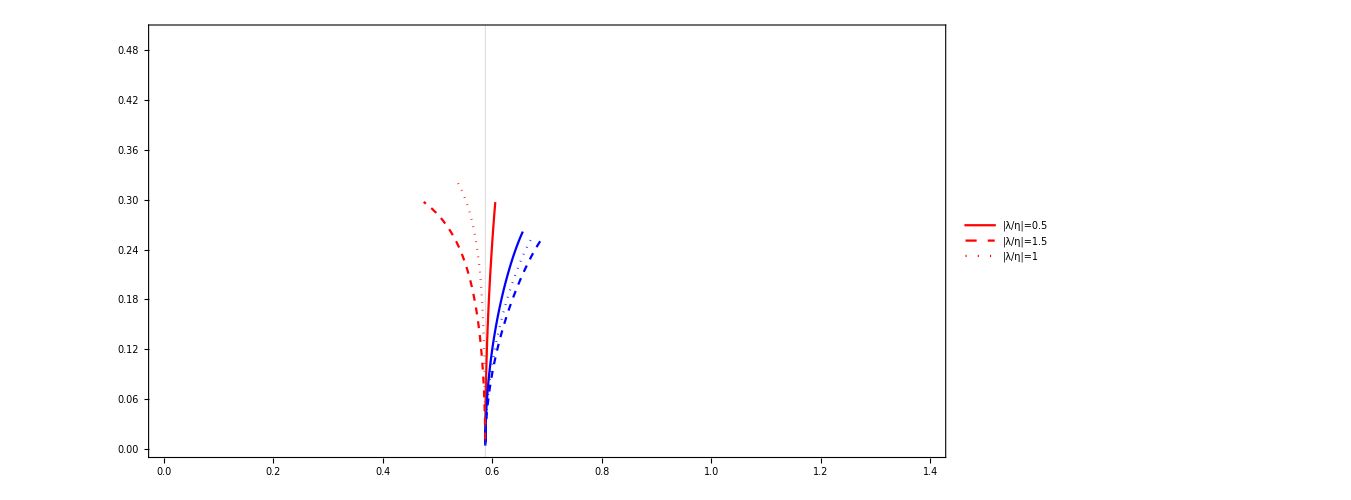
-Graphics-Q/η^(1/2)M/η^(1/2)

```mathematica
Labeled[Show[
ListLinePlot[Legended[QvsM05st,"|λ/η|=0.5"],PlotStyle->Red,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium],PlotRange->{{0,1.4},{0,0.5}},GridLines->{{{verticalline,{Gray,Dashing}}},None}],
ListLinePlot[QvsM05,PlotStyle->Blue,PlotRange->{{0,1.4},{0,0.5}}],
ListLinePlot[QvsM15,PlotStyle->{Blue,Dashed}],
ListLinePlot[Legended[QvsM15st,"|λ/η|=1.5"],PlotStyle->{Red,Dashed}],
ListLinePlot[Legended[QvsM10st,"|λ/η|=1"],PlotStyle->{Red,{Dotted,Thick}}],
ListLinePlot[QvsM10,PlotStyle->{Blue,{Dotted,Thick}}],ImageSize->10^3],
{"Q/η^(1/2)","M/η^(1/2)"},{Left,Bottom}]
```

```mathematica
TAB15st
```